# A mathematical model for universal semantics (Text mining in Russian)

### Weinan E and Yajun Zhou

## Introduction

Accompanying the topic extraction and word translation sections in [1], this Mathematica Notebook file is optimized for v11.0, and it will also run on v10.3 and v10.4. Earlier versions of Mathematica do not contain certain text analysis functionalities required for this program.

Unless explicitly stated otherwise, all the routines (word clustering, word cloud plotting and question answering) below are specifically designed for the current work [1], instead of being imported elsewhere.

[1] W. E and Y. Zhou, “A mathematical model for universal semantics,” 2020, arXiv:1907.12293v6 [cs.CL].

## Preparations

Text corpora mentioned below need to be stored in the following directory (or anywhere else that you redesignate)

```mathematica
SetDirectory["D:\\Documents"]
```

D:\Documents

This Mathematica Notebook file MUST BE executed AFTER all the cells in English.nb are evaluated.

### Pride and Prejudice

The full text for a Russian translation of Jane Austen’s Pride and Prejudice is freely available from lib.ru/INOOLD/OSTEN/gord.txt

After manual cleansing, we save the text as Гордость_и _предубеждение.txt,  which begins with

ГЛАВА I



     Все  знают,  что  молодой  человек,  располагающий  средствами,  должен
подыскивать себе жену.
     Как  бы мало ни были известны намерения и взгляды такого человека после
того,  к

and ends with

ошения.  Дарси, как и
Элизабет,  любил  их по-настоящему.  И  оба  они навсегда сохранили  чувство
горячей благодарности к друзьям, которые привезли ее  в Дербишир и тем самым
способствовали их союзу.

The current Mathematica Notebook demonstrates the analysis of Pride and Prejudice. For the analysis of other texts in our current work, one needs to download text corpora and modify the codes slightly.

### Jane Eyre

The full text  for a Russian translation of Charlotte Brontë’s Jane Eyre is freely available from http://www.lib.ru/INOOLD/BRONTE/janeair.txt

After manual cleansing, the text begins with

Глава I



     В  этот день нечего было и  думать о  прогулке.  Правда,  утром мы  еще
побродили часок по дорожкам облетевшего сада,  но после обеда (когда не было
гостей,  миссис Рид кушала рано

and ends with

еня на
глазах слезы:  он  предвидит свою близкую кончину.  Я  знаю,  что  следующее
письмо, написанное незнакомой рукой, сообщит мне, что господь призвал к себе
своего неутомимого и верного слугу.

### Origin of Species

The full text  for a Russian translation of Charles Darwin’s Origin of Species is freely available from http://darwin-online.org.uk/content/frameset?itemID=F763b&viewtype=text&pageseq=1

After manual cleansing, the text begins with

Глава I ВАРИАЦИИ ПРИ ДОМЕСТИКАЦИИ

Причины изменчивости. Действия привычки и употребления или неупотребления органов. Коррелятивная вариация. Наследственность. Общий характер домашних разновидностей.

and ends with

как наша планета продолжает вращаться согласно неизменным законам тяготения, из такого простого начала развилось и продолжает развиваться бесконечное число самых прекрасных я самых изумительных форм.

Making sure that all the cells in English.nb have been evaluated, you are ready to execute all the cells in this file.

## Russian

Our analysis mainly centers on Russian documents in the modern (post-1918) orthography. Even though some of our working examples come from 19th-century Russian literature, the spellings therein have been thoroughly modernized. We also assume that the Russian documents under investigation do not carry stress marks (which only appear in pedagogical contexts) on individual words. We remove the diacritical mark from ë in the effective spelling.

The following codes run on Mathematica v10.4 or later, as earlier versions may not recognize Cyrillic letters as word characters, thereby failing certain string operations. As of v11.0, Mathematica does not have a built-in function that capitalizes Russian text. This case conversion feature is added to Mathematica v11.1.

```mathematica
ToUpperCase["Все счастливые семьи похожи друг на друга, каждая несчастливая семья несчастлива по-своему."]
```

ВСЕ СЧАСТЛИВЫЕ СЕМЬИ ПОХОЖИ ДРУГ НА ДРУГА, КАЖДАЯ НЕСЧАСТЛИВАЯ СЕМЬЯ НЕСЧАСТЛИВА ПО-СВОЕМУ.

So we need the following routines for switching between lower- and upper-case letters.

```mathematica
RussianToUpperCase[s_]:=StringReplace[s,(x:CharacterRange["а","я"]):>FromCharacterCode[ToCharacterCode[x]-32]]
```

```mathematica
RussianToLowerCase[s_]:=StringReplace[s,(x:CharacterRange["А","Я"]):>FromCharacterCode[ToCharacterCode[x]+32]]
```

```mathematica
RussianToUpperCase["Все счастливые семьи похожи друг на друга, каждая несчастливая семья несчастлива по-своему."]
```

ВСЕ СЧАСТЛИВЫЕ СЕМЬИ ПОХОЖИ ДРУГ НА ДРУГА, КАЖДАЯ НЕСЧАСТЛИВАЯ СЕМЬЯ НЕСЧАСТЛИВА ПО-СВОЕМУ.

For sorting purposes (Mathematica v10.4 or v11.0 does not support multi-level sorting of Russian words), we transliterate the Russian effective spelling and essential root as follows. The transliteration is not meant to be phonetically accurate, but only serves as a convenient one-to-one mapping.

```mathematica
TransliterateFromRussian[w_]:=StringReplace[w,{"а":>"a","б":>"b","в":>"v","г":>"g","д":>"d","е":>"e","ж":>"j","з":>"z","и":>"i","й":>"ï","к":>"k","л":>"l","м":>"m","н":>"n","о":>"o","п":>"p","р":>"r","с":>"s","т":>"t","у":>"u","ф":>"f","х":>"h","ц":>"c","ч":>"q","ш":>"w","щ":>"W","ъ":>"æ","ы":>"y","ь":>"œ","э":>"é","ю":>"û","я":>"â"}]
```

## Russian stop words

We extract the stop word list from the following website

http://snowball.tartarus.org/algorithms/russian/stop.txt

```mathematica
RussianStopWords0={"а","без","более","больше","будет","будто","бы","был","была","были","было","быть","в","вам","вами","вас","вдруг","ведь","весь","во","вот","впрочем","все","всё","всегда","всего","всей","всем","всеми","всему","всех","всею","всю","вся","вы","где","да","даже","для","до","е","его","ее","её","ей","ему","если","есть","еще","ещё","ею","ж","же","за","зачем","здесь","и","из","или","им","ими","иногда","их","к","как","какая","какой","когда","конечно","кто","куда","ли","между","меня","мне","много","мной","мною","может","можно","мой","моя","мы","на","над","надо","наконец","нам","нами","нас","не","него","нее","ней","нельзя","нему","нет","нею","ни","нибудь","никогда","ним","ними","них","ничего","но","ну","нэи","о","об","один","он","она","они","оно","опять","от","перед","по","под","после","потом","потому","почти","при","про","раз","разве","с","сам","сама","сами","самим","самими","самих","само","самого","самой","самом","самому","самою","саму","свою","себе","себя","сейчас","со","собой","собою","совсем","та","так","такой","там","те","тебе","тебя","тем","теми","теперь","тех","то","тобой","тобою","тогда","того","тоже","той","только","том","тому","тот","тою","три","ту","тут","ты","у","уж","уже","хоть","хотя","чего","чем","через","что","чтоб","чтобы","чуть","эи","эта","эти","этим","этими","этих","это","этого","этой","этом","этому","этот","этою","эту","эты","я"};
```

and remove

```mathematica
{"кажется","сказал","сказала","сказать","хорошо","человек","говорил","жизнь","сегодня"}
```

{кажется,сказал,сказала,сказать,хорошо,человек,говорил,жизнь,сегодня}

and make a few changes.

```mathematica
mostRussian={"самая","самое","самоё","самой","самом","самою","самую","самые","самый","самым","самых","самого","самому","самыми"};
```

```mathematica
beRussian={"бывшая","бывшее","бывшей","бывшем","бывшею","бывшие","бывший","бывшим","бывших","бывшую","бывшего","бывшему","бывшим","будем","будем","будет","будет","будете","будете","будешь","будешь","буду","буду","будут","будут","будучи","будь","будьте","быв","бывав","бывавши","бывавший","бываем","бывает","бываете","бываешь","бывай","бывайте","бывал","бывала","бывали","бывало","бывать","бывать","бывать","бывать","бывать","бывать","бывать","бываю","бывают","бывающий","бывая","бывши","бывший","был","была","были","было","быть","еси","есмы","есмь","есте","есть","суть","сущий","сущая","сущее","сущей","сущем","сущею","сущие","сущий","сущим","сущих","сущую","сущего","сущему","сущими"};
```

```mathematica
whoRussian={"кем","кого","кого","ком","кому","кто"};
```

```mathematica
whichRussian={"которая","которое","которой","котором","которою","которую","которые","который","которым","которых","которого","которому","которыми"};
```

```mathematica
whoseRussian={"чей","чье","чьё","чьём","чьего","чьей","чьем","чьему","чьею","чьи","чьим","чьими","чьих","чью","чья"};
```

```mathematica
whatRussian={"чего","чем","чём","чему","что"};
```

```mathematica
whatkindRussian={"какая","какие","каким","какими","каких","какого","какое","какой","каком","какому","какою","какую"};
```

```mathematica
posspronRussian={"ваш","ваша","ваше","вашего","вашей","вашем","вашему","вашею","ваши","вашим","вашими","ваших","вашу","мое","моё","моего","моей","моем","моему","моею","мои","моим","моими","моих","мой","мою","моя","наш","наша","наше","нашего","нашей","нашем","нашему","нашею","наши","нашим","нашими","наших","нашу","свое","своё","своего","своей","своем","своему","своею","свои","своим","своими","своих","свой","свою","своя","твое","твоё","твоего","твоей","твоем","твоему","твоею","твои","твоим","твоими","твоих","твой","твою","твоя"};
```

```mathematica
everyRussian={"каждая","каждого","каждое","каждой","каждом","каждому","каждою","каждую","каждые","каждый","каждым","каждыми","каждых"};
```

```mathematica
otherRussian={"другая","другие","другим","других","другое","другой","другом","другою","другую","другими","другого","другому"}∪{"иная","иное","иной","ином","иною","иную","иные","иным","иных","иначе","иного","иному","иными"};
```

```mathematica
oneRussian={"один","одна","одни","одно","одну","одним","одних","одной","одном","одною","одними","одного","одному"};
```

```mathematica
mayRussian={"мог","моги","могу","могла","могли","могло","могут","можем","может","могите","могшая","могшее","могшей","могшем","могшею","могшие","могший","могшим","могших","могшую","можете","можешь","могущая","могущее","могущей","могущем","могущею","могущие","могущий","могущим","могущих","могущую","могшего","могшему","могшими","могущего","могущему","могущими"};
```

```mathematica
doRussian={"делав","делай","делал","делан","делаю","делая","делаем","делает","делала","делали","делало","делана","делано","деланы","делать","делают","сделав","сделай","сделал","сделан","сделаю","делавши","делаема","делаемо","делаемы","делаете","делаешь","делайте","сделаем","сделает","сделала","сделали","сделало","сделана","сделано","сделаны","сделать","сделают","делавшая","делавшее","делавшей","делавшем","делавшею","делавшие","делавший","делавшим","делавших","делавшую","делаемая","делаемое","делаемой","делаемом","делаемою","делаемую","делаемые","делаемый","делаемым","делаемых","деланная","деланное","деланной","деланном","деланною","деланную","деланные","деланный","деланным","деланных","делающая","делающее","делающей","делающем","делающею","делающие","делающий","делающим","делающих","делающую","сделавши","сделаете","сделаешь","сделайте","делавшего","делавшему","делавшими","делаемого","делаемому","делаемыми","деланного","деланному","деланными","делающего","делающему","делающими","сделавшая","сделавшее","сделавшей","сделавшем","сделавшею","сделавшие","сделавший","сделавшим","сделавших","сделавшую","сделанная","сделанное","сделанной","сделанном","сделанною","сделанную","сделанные","сделанный","сделанным","сделанных","сделавшего","сделавшему","сделавшими","сделанного","сделанному","сделанными"};
```

```mathematica
bothRussian={"оба","обе","обеим","обеих","обоим","обоих","обеими","обоего","обоими"};
```

```mathematica
whateverRussian={"никакая","никакие","никаким","никаких","никакое","никакой","никаком","никакою","никакую","никакими","никакого","никакому"};
```

```mathematica
suchRussian={"такая","такие","таким","таких","такое","такой","таком","такою","такую","такими","такого","такому"};
```

```mathematica
RussianStopWords=RussianStopWords0∪beRussian∪whoRussian∪whoseRussian∪whichRussian∪whatRussian∪whatkindRussian∪posspronRussian∪everyRussian∪otherRussian∪oneRussian∪mayRussian∪doRussian∪bothRussian∪whateverRussian∪suchRussian∪{"около"}∪{"вместе","вместо"}∪{"обо","ото","изо"}∪{"менее"}∪{"сам","сама","сами","само","саму","самая","самим","самих","самое","самой","самом","самою","самую","самые","самый","самым","самых","самими","самого","самому","самыми","самоё","самое"}∪{"столь"}∪{"сей","сею","сии","сим","сих","сию","сия","сём","сем","сего","сему","сими","сие","сё","се"}∪{"ко"}∪{"однако"}∪{"слишком"}∪{"кроме"}∪{"нечего","негде","некогда","некуда","некого","ничего","никто","нигде","никак","никуда","ниоткуда","нисколько","ничто"}∪{"насколько"}∪{"пусть"}∪{"м"}∪{"очень"}∪{"часто"}∪{"поныне"}∪{"некоторая","некоторое","некоторой","некотором","некоторою","некоторую","некоторые","некоторый","некоторым","некоторых","несколько","некоторого","некоторому","некоторыми","нескольким","нескольких","несколькими"}∪{"настолько","столь"}∪{"откуда","отсюда","оттуда","сюда","туда"}∪{"б"}∪{"пусть"}∪mostRussian∪{"скоро"}∪{"неужели","вовсе","вон","лишь","словно","именно","давай","пускай","давайте","дай","дайте","ка"}∪{"также","зато","прежде","поскольку","оттого","несмотря","точно","чём"}∪{"возле","вокруг","внутри","посреди","среди","впереди","позади","сквозь","спустя","вдоль","против","напротив","навстречу","вопреки","согласно","вслед","кое","никого","никому","никем","некому","некем","ничему","ничем","нечему","нечем"}∪{"ничей","ничьи","ничью","ничья","ничьё","ничьей","ничьею","ничьим","ничьих","ничьём","никакая","никакие","никаким","никаких","никакое","никакой","никаком","никакою","никакую","ничьего","ничьему","ничьими","никакими","никакого","никакому"}∪{"любая","любое","любой","любом","любою","любую","любые","любым","любых","любого","любому","любыми"}∪{"всяк","всяка","всяки","всяко","всякая","всякие","всякий","всяким","всяких","всякое","всякой","всяком","всякою","всякую","всякими","всякого","всякому"}∪{"каков","какова","каково","каковы","подле","вне","вовне","сколь","вскоре","весьма"}∪{"сколько","скольким","скольких","сколькими"}∪{"почему","отчего","зачем"}∪{"нем","нём","неё","снова","должен","должна","должно","должны","пожалуй","почем","почём","пока","притом","напролёт","напролет","поэтому"}∪{"кое","кои","кой","кою","коя","коей","коем","коею","коим","коих","коего","коему","коими"}∪{"каков","какова","каково","каковы","каковая","каковое","каковой","каковом","каковою","каковую","каковые","каковым","каковых","какового","каковому","каковыми","отнюдь","нередко"}∪{"столько","стольким","стольких","столькими"}∪{"таки","таков","таково","такова","таковы"}∪{"либо","ныне","едва","ибо","наиболее"}∪{"назад","взад","еле"}∪{"мног","многа","многи","много","многая","многие","многий","многим","многих","многое","многой","многом","многою","многую","многими","многого","многому"}∪{"немног","немнога","немноги","немного","немногая","немногие","немногий","немногим","немногих","немногое","немногой","немногом","немногою","немногую","немногими","немногого","немногому"}∪{"затем"};
```

## Russian test words

Most Russian nouns distinguish six cases (nominative, genitive, dative, accusative, instrumental, prepositional) in singular and plural. A limited number of nouns have additional forms in three more cases (vocative, locative and partitive).

The sample nouns below are chosen according to the following web pages:

https://en.wiktionary.org/wiki/Appendix:Russian_nouns#Declension_paradigms

https://en.wiktionary.org/wiki/Template:ru-noun-table#Basic_examples

Unlike Polish, the consonants of the Russian noun stem mostly remain stable in all declined forms.

```mathematica
appearanceRussian={"вид","вида","виде","виду","виды","видам","видах","видов","видом","видами"};
```

```mathematica
magazineRussian={"журнал","журнала","журнале","журналу","журналы","журналам","журналах","журналов","журналом","журналами"};
```

```mathematica
fatherRussian={"отец","отца","отце","отцу","отцы","отцам","отцах","отцов","отцом","отцами"};
```

```mathematica
tableRussian={"стол","стола","столе","столу","столы","столам","столах","столов","столом","столами"};
```

```mathematica
dishRussian={"блюд","блюда","блюде","блюдо","блюду","блюдам","блюдах","блюдом","блюдами"};
```

```mathematica
dwellingRussian={"жилищ","жилища","жилище","жилищу","жилищам","жилищах","жилищем","жилищами"};
```

```mathematica
windowRussian={"окна","окне","окно","окну","окон","окнам","окнах","окном","окнами"};
```

```mathematica
letterRussian={"писем","письма","письме","письмо","письму","письмам","письмах","письмом","письмами"};
```

```mathematica
collegeRussian={"училищ","училища","училище","училищу","училищам","училищах","училищем","училищами"};
```

```mathematica
newspaperRussian={"газет","газета","газете","газету","газеты","газетам","газетах","газетой","газетою","газетами"};
```

```mathematica
taskRussian={"работ","работа","работе","работу","работы","работам","работах","работой","работою","работами"};
```

```mathematica
sisterRussian={"сестра","сестре","сестру","сестры","сестёр","сёстры","сестрой","сестрою","сёстрам","сёстрах","сёстрами"};
```

```mathematica
godRussian={"бог","бога","боге","боги","богу","боже","богам","богах","богов","богом","богами"};
```

```mathematica
pencilRussian={"карандаш","карандаша","карандаше","карандаши","карандашу","карандашам","карандашах","карандашей","карандашом","карандашами"};
```

```mathematica
knifeRussian={"нож","ножа","ноже","ножи","ножу","ножам","ножах","ножей","ножом","ножами"};
```

```mathematica
comradeRussian={"товарищ","товарища","товарище","товарищи","товарищу","товарищам","товарищах","товарищей","товарищем","товарищами"};
```

```mathematica
lessonRussian={"урок","урока","уроке","уроки","уроку","урокам","уроках","уроков","уроком","уроками"};
```

```mathematica
bookRussian={"книг","книга","книге","книги","книгу","книгам","книгах","книгой","книгою","книгами"};
```

```mathematica
kopekRussian={"копеек","копейка","копейке","копейки","копейку","копейкам","копейках","копейкой","копейкою","копейками"};
```

```mathematica
AprilRussian={"апреле","апрели","апрель","апрелю","апреля","апрелей","апрелем","апрелям","апрелях","апрелями"};
```

```mathematica
heroRussian={"герое","герои","герой","герою","героя","героев","героем","героям","героях","героями"};
```

```mathematica
dayRussian={"дне","дни","дню","дня","день","дней","дням","днях","днём","днями"};
```

```mathematica
dictionaryRussian={"словаре","словари","словарь","словарю","словаря","словарей","словарям","словарях","словарём","словарями"};
```

```mathematica
eventRussian={"случае","случаи","случай","случаю","случая","случаев","случаем","случаям","случаях","случаями"};
```

```mathematica
teacherRussian={"учителе","учители","учитель","учителю","учителя","учителей","учителем","учителям","учителях","учителями"};
```

```mathematica
teaRussian={"чае","чаи","чай","чаю","чая","чаем","чаям","чаях","чаёв","чаями"};
```

```mathematica
timeRussian={"время","времён","времена","времени","временам","временах","временем","временами"};
```

```mathematica
seaRussian={"море","морю","моря","морей","морем","морям","морях","морями"};
```

```mathematica
fieldRussian={"поле","полю","поля","полей","полем","полям","полях","полями"};
```

```mathematica
learningRussian={"учение","учении","учений","учению","учения","учением","учениям","учениях","учениями"};
```

```mathematica
doorRussian={"двери","дверь","дверей","дверью","дверям","дверях","дверьми","дверями"};
```

```mathematica
historyRussian={"истории","историй","историю","история","историей","историею","историям","историях","историями"};
```

```mathematica
horseRussian={"лошади","лошадь","лошадей","лошадью","лошадям","лошадях","лошадьми","лошадями"};
```

```mathematica
weekRussian={"неделе","недели","недель","неделю","неделя","неделей","неделею","неделям","неделях","неделями"};
```

```mathematica
nurseRussian={"няне","няни","нянь","няню","няня","няней","нянею","няням","нянях","нянями"};
```

```mathematica
haloRussian={"ореол","ореола","ореоле","ореолу","ореолы","ореолам","ореолах","ореолов","ореолом","ореолами"};
```

```mathematica
lifeRussian={"житие","житии","житий","житию","жития","житием","житиям","житиях","житиями"};
```

```mathematica
headRussian={"голов","голова","голове","голову","головы","головам","головах","головой","головою","головами"};
```

```mathematica
boyarRussian={"бояр","бояре","боярам","боярах","боярин","боярами","боярина","боярине","боярину","боярином"};
```

```mathematica
squareRussian={"площади","площадь","площадей","площадью","площадям","площадях","площадями"};
```

```mathematica
heterosexualityRussian={"гетеросексуальности","гетеросексуальность","гетеросексуальностью"};
```

```mathematica
maidenRussian={"дев","дева","деве","дево","деву","девы","девам","девах","девой","девою","девами"};
```

```mathematica
featherRussian={"пух","пуха","пухе","пуху","пухом"};
```

```mathematica
fingerRussian={"палец","пальца","пальце","пальцу","пальцы","пальцам","пальцах","пальцев","пальцем","пальцами"};
```

```mathematica
wicketRussian={"воротец","воротца","воротцам","воротцах","воротцами"};
```

```mathematica
pupilRussian={"учащемся","учащиеся","учащийся","учащимся","учащихся","учащегося","учащемуся","учащимися"};
```

```mathematica
lakeRussian={"озерца","озерце","озерцо","озерцу","озёрец","озёрца","озерцом","озёрцам","озёрцах","озёрцами"};
```

```mathematica
glandRussian={"желёз","железа","железе","железу","железы","железам","железах","железой","железою","железами"};
```

```mathematica
snowRussian={"снег","снега","снеге","снегу","снегам","снегах","снегов","снегом","снегами"};
```

```mathematica
sparkRussian={"искр","искра","искре","искру","искры","искрам","искрах","искрой","искрою","искрами"};
```

```mathematica
praiseRussian={"хвала","хвале","хвалу","хвалы","хвалам","хвалах","хвалой","хвалою","хвалами"};
```

```mathematica
reinRussian={"повод","повода","поводе","поводу","поводом","поводья","поводьев","поводьям","поводьях","поводьями"};
```

```mathematica
maturewolfRussian={"волчищ","волчища","волчище","волчищи","волчищу","волчищам","волчищах","волчищей","волчищем","волчищами"};
```

```mathematica
bridgeRussian={"мост","моста","мосте","мосту","мосты","мостам","мостах","мостов","мостом","мостами"};
```

```mathematica
phenomenonRussian={"феномен","феномена","феномене","феномену","феномены","феноменам","феноменах","феноменов","феноменом","феноменами"};
```

```mathematica
ragRussian={"лоскут","лоскута","лоскуте","лоскуту","лоскуты","лоскутам","лоскутах","лоскутов","лоскутом","лоскутья","лоскутами","лоскутьев","лоскутьям","лоскутьях","лоскутьями"};
```

```mathematica
littleboyRussian={"мальчат","мальчата","мальчатам","мальчатах","мальчонка","мальчонке","мальчонки","мальчонку","мальчонок","мальчатами","мальчонкам","мальчонках","мальчонков","мальчонком","мальчонками"};
```

```mathematica
bootRussian={"сапожек","сапожка","сапожке","сапожки","сапожку","сапожок","сапожкам","сапожках","сапожков","сапожком","сапожками"};
```

```mathematica
kneeRussian={"колена","колене","колени","колено","колену","коленей","коленом","коленям","коленях","коленями"};
```

```mathematica
tribeRussian={"колен","колена","колене","колено","колену","коленам","коленах","коленом","коленами"};
```

```mathematica
jointRussian={"колена","колене","колено","колену","коленом","коленья","коленьев","коленьям","коленьях","коленьями"};
```

```mathematica
stoneRussian={"камне","камни","камню","камня","камень","камней","камнем","камням","камнях","каменья","камнями","каменьев","каменьям","каменьях","каменьями"};
```

```mathematica
childRussian={"дети","детей","детям","детях","ребят","детьми","ребята","ребятам","ребятах","ребёнка","ребёнке","ребёнку","ребёнок","ребятами","ребёнком"};
```

```mathematica
mouthRussian={"рот","рта","рте","рту","рты","ртам","ртах","ртов","ртом","ртами"};
```

```mathematica
iceRussian={"лёд","льда","льде","льду","льды","льдам","льдах","льдов","льдом","льдами"};
```

```mathematica
friendRussian={"друг","друга","друге","другу","друже","другом","друзей","друзья","друзьям","друзьях","друзьями"};
```

```mathematica
sonRussian={"сын","сына","сыне","сыну","сыны","сынам","сынах","сынов","сыном","сынами","сыновей","сыновья","сыновьям","сыновьях","сыновьями"};
```

```mathematica
dreamRussian={"сна","сне","сну","сны","сон","снам","снах","снов","сном","снами"};
```

```mathematica
husbandRussian={"муж","мужа","муже","мужу","мужей","мужем","мужья","мужьям","мужьях","мужьями"};
```

```mathematica
RussianSampleNouns=appearanceRussian∪magazineRussian∪fatherRussian∪tableRussian∪dishRussian∪dwellingRussian∪windowRussian∪letterRussian∪collegeRussian∪newspaperRussian∪taskRussian∪sisterRussian∪godRussian∪pencilRussian∪knifeRussian∪comradeRussian∪lessonRussian∪bookRussian∪kopekRussian∪AprilRussian∪heroRussian∪dayRussian∪dictionaryRussian∪eventRussian∪teacherRussian∪teaRussian∪timeRussian∪seaRussian∪fieldRussian∪learningRussian∪doorRussian∪historyRussian∪horseRussian∪weekRussian∪nurseRussian∪haloRussian∪lifeRussian∪headRussian∪boyarRussian∪squareRussian∪heterosexualityRussian∪maidenRussian∪featherRussian∪fingerRussian∪wicketRussian∪pupilRussian∪lakeRussian∪glandRussian∪snowRussian∪sparkRussian∪praiseRussian∪reinRussian∪maturewolfRussian∪bridgeRussian∪phenomenonRussian∪ragRussian∪littleboyRussian∪bootRussian∪kneeRussian∪tribeRussian∪jointRussian∪stoneRussian∪childRussian∪mouthRussian∪iceRussian∪friendRussian∪sonRussian∪dreamRussian∪husbandRussian;
```

Consonants in the stem of a Russian adjective remain inert, except in comparatives. We list below some typical Russian adjectives (including certain adjectival participles of verbs) that may or may not incur consonant alternation in the stem.

```mathematica
bigRussian={"велик","велика","велики","велико","большая","большие","большим","больших","большое","большой","большом","большою","большую","большими","большого","большому"}∪{"большая","большее","большей","большем","большею","большие","больший","большим","больших","большую","большего","большему","большими"}∪{"наибольшая","наибольшее","наибольшей","наибольшем","наибольшею","наибольшие","наибольший","наибольшим","наибольших","наибольшую","наибольшего","наибольшему","наибольшими"};
```

```mathematica
beautifulRussian={"красив","красива","красиво","красивы","красивая","красивое","красивой","красивом","красивою","красивую","красивые","красивый","красивым","красивых","красивого","красивому","красивыми"}∪{"красивее"}∪{"краше"}∪{"красивейший"};
```

```mathematica
youngRussian={"молод","молода","молодо","молоды","молодая","молодое","молодой","молодом","молодою","молодую","молодые","молодым","молодых","молодого","молодому","молодыми"}∪{"моложе"};
```

```mathematica
expensiveRussian={"дорог","дорога","дороги","дорого","дорогая","дорогие","дорогим","дорогих","дорогое","дорогой","дорогом","дорогою","дорогую","дорогими","дорогого","дорогому"}∪{"дороже"};
```

```mathematica
softRussian={"мягка","мягки","мягко","мягок","мягкая","мягкие","мягкий","мягким","мягких","мягкое","мягкой","мягком","мягкою","мягкую","мягкими","мягкого","мягкому"}∪{"мягче"}∪{"мягчайший","наимягчайший"};
```

```mathematica
steepRussian={"крут","крута","круто","круты","крутая","крутое","крутой","крутом","крутою","крутую","крутые","крутым","крутых","крутого","крутому","крутыми"}∪{"круче"}∪{"крутейший"};
```

```mathematica
silentRussian={"тих","тиха","тихи","тихо","тихая","тихие","тихий","тихим","тихих","тихое","тихой","тихом","тихою","тихую","тихими","тихого","тихому"}∪{"тише"}∪{"тишайший"};
```

```mathematica
frequentRussian={"част","часта","часто","часты","частая","частое","частой","частом","частою","частую","частые","частый","частым","частых","частого","частому","частыми"}∪{"чаще"};
```

```mathematica
smoothRussian={"гладка","гладки","гладко","гладок","гладкая","гладкие","гладкий","гладким","гладких","гладкое","гладкой","гладком","гладкою","гладкую","гладкими","гладкого","гладкому"}∪{"глаже"}∪{"гладчайший"};
```

```mathematica
doRussianPresentActiveParticiple={"делающая","делающее","делающей","делающем","делающею","делающие","делающий","делающим","делающих","делающую","делающего","делающему","делающими"};
```

```mathematica
doRussianPastActiveParticiple={"делавшая","делавшее","делавшей","делавшем","делавшею","делавшие","делавший","делавшим","делавших","делавшую","делавшего","делавшему","делавшими"};
```

```mathematica
loveRussianPresentPassiveParticiple={"любим","любима","любимо","любимы","любимая","любимое","любимой","любимом","любимою","любимую","любимые","любимый","любимым","любимых","любимого","любимому","любимыми"};
```

```mathematica
decideRussianPastPassivePerfectParticiple={"решён","решена","решено","решены","решённая","решённое","решённой","решённом","решённою","решённую","решённые","решённый","решённым","решённых","решённого","решённому","решёнными"};
```

```mathematica
RussianSampleAdjectives=bigRussian∪beautifulRussian∪youngRussian∪expensiveRussian∪softRussian∪steepRussian∪silentRussian∪frequentRussian∪doRussianPresentActiveParticiple∪doRussianPastActiveParticiple∪loveRussianPresentPassiveParticiple∪decideRussianPastPassivePerfectParticiple;
```

Like Polish, a great majority of Russian verbs come in imperfective/perfective pairs. Consonant alternations still find their way into the Russian verb stems (more precisely, the end of stems) in conjugated forms. In the following, we list representative verbs from all the 16 Zaliznyak classes (https://en.wiktionary.org/wiki/Appendix:Russian_verbs), together with their imperfective/perfective counterparts that are formed in various ways (we note that the two aspects of the same verb may not belong to the same Zaliznyak class). These verb conjugations may also involve consonant changes in the stem, or other types of irregularities.

```mathematica
Zaliznyak♯1♯do={"делав","делай","делал","делаю","делая","делаем","делает","делала","делали","делало","делать","делают","делавши","делаете","делаешь","делайте","делавший","делаемый","деланный","делающий"}∪{"сделав","сделай","сделал","сделаю","сделаем","сделает","сделала","сделали","сделало","сделать","сделают","сделавши","сделаете","сделаешь","сделайте","сделавший","сделанный"};
```

```mathematica
Zaliznyak♯2a♯draw={"рисуй","рисую","рисуя","рисуем","рисует","рисуют","рисовав","рисовал","рисуете","рисуешь","рисуйте","рисовала","рисовали","рисовало","рисовать","рисуемый","рисующий","рисовавши","рисовавший","рисованный"}∪{"нарисуй","нарисую","нарисуем","нарисует","нарисуют","нарисовав","нарисовал","нарисуете","нарисуешь","нарисуйте","нарисовала","нарисовали","нарисовало","нарисовать","нарисовавши","нарисовавший","нарисованный"};
```

```mathematica
Zaliznyak♯2b♯vomit={"блюй","блюю","блюя","блюют","блюём","блюёт","блевав","блевал","блюйте","блюёте","блюёшь","блевала","блевали","блевало","блевать","блюющий","блевавши","блевавший","блёванный"}∪{"блевани","блевану","блеванув","блеванул","блеванут","блеванём","блеванёт","блеваните","блеванула","блеванули","блевануло","блевануть","блеванёте","блеванёшь","блеванувши","блеванувший"};
```

```mathematica
Zaliznyak♯3a♯die={"гиб","гибла","гибли","гибло","гибни","гибну","гибнем","гибнет","гибнув","гибнул","гибнут","гибнете","гибнешь","гибните","гибнуть","гибнувши","гибнущий","гибнувший"}∪{"погиб","погибла","погибли","погибло","погибни","погибну","погибши","погибнем","погибнет","погибнут","погибший","погибнете","погибнешь","погибните","погибнуть"};
```

```mathematica
Zaliznyak♯3b♯risk={"рискни","рискну","рискнув","рискнул","рискнут","рискнём","рискнёт","рискните","рискнула","рискнули","рискнуло","рискнуть","рискнёте","рискнёшь","рискнувши","рискнувший"}∪{"рискуй","рискую","рискуя","рискуем","рискует","рискуют","рисковав","рисковал","рискуете","рискуешь","рискуйте","рисковала","рисковали","рисковало","рисковать","рискующий","рисковавши","рисковавший"};
```

```mathematica
Zaliznyak♯3c♯glance={"взгляни","взгляну","взглянем","взглянет","взглянув","взглянул","взглянут","взглянете","взглянешь","взгляните","взглянула","взглянули","взглянуло","взглянуть","взглянувши","взглянувший"}∪{"гляди","глядя","гляжу","глядев","глядел","глядим","глядит","глядят","глядела","глядели","глядело","глядеть","глядите","глядишь","глядевши","глядящий","глядевший"}∪{"взглядывав","взглядывай","взглядывал","взглядываю","взглядывая","взглядываем","взглядывает","взглядывала","взглядывали","взглядывало","взглядывать","взглядывают","взглядывавши","взглядываете","взглядываешь","взглядывайте","взглядывавший","взглядываемый","взглядывающий"};
```

```mathematica
Zaliznyak♯4a♯sting={"жаль","жалю","жаля","жалив","жалил","жалим","жалит","жалят","жалила","жалили","жалило","жалите","жалить","жалишь","жальте","жаливши","жалимый","жалящий","жаленный","жаливший"}∪{"ужаль","ужалю","ужалив","ужалил","ужалим","ужалит","ужалят","ужалила","ужалили","ужалило","ужалите","ужалить","ужалишь","ужальте","ужаливши","ужаленный","ужаливший"};
```

```mathematica
Zaliznyak♯4b♯spare={"щади","щадя","щажу","щадив","щадил","щадим","щадит","щадят","щадила","щадили","щадило","щадите","щадить","щадишь","щадивши","щадимый","щадящий","щадивший","щажённый"}∪{"пощади","пощажу","пощадив","пощадил","пощадим","пощадит","пощадят","пощадила","пощадили","пощадило","пощадите","пощадить","пощадишь","пощадивши","пощадивший","пощажённый"};
```

```mathematica
Zaliznyak♯4c♯love={"люби","любя","любив","любил","любим","любит","люблю","любят","любила","любили","любило","любите","любить","любишь","любивши","любимый","любящий","любивший","любленный"}∪{"полюби","полюбив","полюбил","полюбим","полюбит","полюблю","полюбят","полюбила","полюбили","полюбило","полюбите","полюбить","полюбишь","полюбивши","полюбивший","полюбленный"};
```

```mathematica
Zaliznyak♯5a♯hear={"слыша","слышу","слышав","слышал","слышат","слышим","слышит","слышала","слышали","слышало","слышать","слышите","слышишь","слышавши","слышащий","слышимый","слышавший","слышанный"}∪{"услышу","услышь","услышав","услышал","услышат","услышим","услышит","услышала","услышали","услышало","услышать","услышите","услышишь","услышьте","услышавши","услышавший","услышанный"};
```

```mathematica
Zaliznyak♯5b♯jingle={"бренча","бренчи","бренчу","бренчав","бренчал","бренчат","бренчим","бренчит","бренчала","бренчали","бренчало","бренчать","бренчите","бренчишь","бренчавши","бренчащий","бренчавший"};
```

```mathematica
Zaliznyak♯5c♯banish={"изгнав","изгнал","изгони","изгоню","изгнала","изгнали","изгнало","изгнать","изгоним","изгонит","изгонят","изгнавши","изгоните","изгонишь","изгнавший","изгнанный"}∪{"изгоняв","изгоняй","изгонял","изгоняю","изгоняя","изгоняем","изгоняет","изгоняла","изгоняли","изгоняло","изгонять","изгоняют","изгонявши","изгоняете","изгоняешь","изгоняйте","изгонявший","изгоняемый","изгоняющий"};
```

```mathematica
Zaliznyak♯6a♯flutter={"вей","вею","вея","веем","веет","веют","веяв","веял","веете","веешь","вейте","веяла","веяли","веяло","веять","веемый","веющий","веявши","веявший","веянный"};
```

```mathematica
Zaliznyak♯6b♯appeal={"воззвав","воззвал","воззови","воззову","воззвала","воззвали","воззвало","воззвать","воззовут","воззовём","воззовёт","воззвавши","воззовите","воззовёте","воззовёшь","воззвавший","воззванный"}∪{"взывав","взывай","взывал","взываю","взывая","взываем","взывает","взывала","взывали","взывало","взывать","взывают","взывавши","взываете","взываешь","взывайте","взывавший","взывающий"};
```

```mathematica
Zaliznyak♯6c♯recover={"взыщи","взыщу","взыщем","взыщет","взыщут","взыскав","взыскал","взыщете","взыщешь","взыщите","взыскала","взыскали","взыскало","взыскать","взыскавши","взыскавший","взысканный"}∪{"взыскивав","взыскивай","взыскивал","взыскиваю","взыскивая","взыскиваем","взыскивает","взыскивала","взыскивали","взыскивало","взыскивать","взыскивают","взыскивавши","взыскиваете","взыскиваешь","взыскивайте","взыскивавший","взыскиваемый","взыскивающий"};
```

```mathematica
Zaliznyak♯7a♯meddle={"влез","влезу","влезь","влезем","влезет","влезла","влезли","влезло","влезть","влезут","влезши","влезете","влезешь","влезший","влезьте"}∪{"влезав","влезай","влезал","влезаю","влезая","влезаем","влезает","влезала","влезали","влезало","влезать","влезают","влезавши","влезаете","влезаешь","влезайте","влезавший","влезающий"};
```

```mathematica
Zaliznyak♯7b♯lead={"веди","веду","ведя","вела","вели","вело","ведут","ведши","ведём","ведёт","вести","ведите","ведший","ведёте","ведёшь","ведомый","ведущий","ведённый"}∪{"поведи","поведу","поведя","повела","повели","повело","поведут","поведши","поведём","поведёт","повести","поведите","поведший","поведёте","поведёшь","поведённый"};
```

```mathematica
Zaliznyak♯8a♯leak={"вытек","вытеки","вытеку","вытечь","вытекла","вытекли","вытекло","вытекут","вытекши","вытечем","вытечет","вытеките","вытекший","вытечете","вытечешь"}∪{"вытекав","вытекай","вытекал","вытекаю","вытекая","вытекаем","вытекает","вытекала","вытекали","вытекало","вытекать","вытекают","вытекавши","вытекаете","вытекаешь","вытекайте","вытекавший","вытекающий"}∪{"тёк","теки","теку","течь","текла","текли","текло","текут","течём","течёт","тёкши","теките","течёте","течёшь","тёкший","текущий"};
```

```mathematica
Zaliznyak♯8b♯guard={"берёг","береги","берегу","беречь","берегла","берегли","берегло","берегут","бережём","бережёт","берёгши","берегите","бережёте","бережёшь","берёгший","берегущий","бережённый"}∪{"сберёг","сбереги","сберегу","сберечь","сберегла","сберегли","сберегло","сберегут","сбережём","сбережёт","сберёгши","сберегите","сбережёте","сбережёшь","сберёгший","сбережённый"}∪{"уберёг","убереги","уберегу","уберечь","уберегла","уберегли","уберегло","уберегут","убережём","убережёт","уберёгши","уберегите","убережёте","убережёшь","уберёгший","убережённый"};
```

```mathematica
Zaliznyak♯9a♯becomeextinct={"вымер","вымри","вымру","вымрем","вымрет","вымрут","вымерев","вымерла","вымерли","вымерло","вымерши","вымрете","вымрешь","вымрите","вымереть","вымерший"}∪{"вымирав","вымирай","вымирал","вымираю","вымирая","вымираем","вымирает","вымирала","вымирали","вымирало","вымирать","вымирают","вымиравши","вымираете","вымираешь","вымирайте","вымиравший","вымирающий"};
```

```mathematica
Zaliznyak♯9b♯rub={"три","тру","тёр","трут","трём","трёт","трите","трёте","трёшь","тёрла","тёрли","тёрло","тёрши","тереть","трущий","тёртый","тёрший"}∪{"потри","потру","потёр","потрут","потрём","потрёт","потерев","потрите","потрёте","потрёшь","потёрла","потёрли","потёрло","потёрши","потереть","потёртый","потёрший"};
```

```mathematica
Zaliznyak♯10a♯weed={"выполи","выполю","выполем","выполет","выполов","выполол","выполют","выполете","выполешь","выполите","выполола","выпололи","выпололо","выполоть","выполовши","выполотый","выполовший"}∪{"выпалывав","выпалывай","выпалывал","выпалываю","выпалывая","выпалываем","выпалывает","выпалывала","выпалывали","выпалывало","выпалывать","выпалывают","выпалывавши","выпалываете","выпалываешь","выпалывайте","выпалывавший","выпалываемый","выпалывающий"};
```

There are no class 10b verbs.

```mathematica
Zaliznyak♯10c♯stick={"вколи","вколю","вколем","вколет","вколов","вколол","вколют","вколете","вколешь","вколите","вколола","вкололи","вкололо","вколоть","вколовши","вколотый","вколовший"}∪{"вкалывав","вкалывай","вкалывал","вкалываю","вкалывая","вкалываем","вкалывает","вкалывала","вкалывали","вкалывало","вкалывать","вкалывают","вкалывавши","вкалываете","вкалываешь","вкалывайте","вкалывавший","вкалываемый","вкалывающий"};
```

```mathematica
Zaliznyak♯11a♯spillover={"вылейся","вылился","выльюсь","вылилась","вылились","вылилось","вылиться","выльемся","выльется","выльются","вылейтесь","вылившись","выльетесь","выльешься","вылившийся"}∪{"выливайся","выливался","выливаюсь","выливаясь","выливаемся","выливается","выливалась","выливались","выливалось","выливаться","выливаются","выливавшись","выливаетесь","выливаешься","выливайтесь","выливавшийся","выливающийся"};
```

```mathematica
Zaliznyak♯11b♯crush={"добей","добив","добил","добью","добила","добили","добило","добить","добьют","добьём","добьёт","добейте","добивши","добитый","добьёте","добьёшь","добивший"}∪{"добивав","добивай","добивал","добиваю","добивая","добиваем","добивает","добивала","добивали","добивало","добивать","добивают","добивавши","добиваете","добиваешь","добивайте","добивавший","добиваемый","добивающий"};
```

```mathematica
Zaliznyak♯12a♯wash={"мой","мою","моя","мыв","мыл","моем","моет","моют","мыла","мыли","мыло","мыть","моете","моешь","мойте","мывши","мытый","моемый","моющий","мывший"}∪{"помой","помою","помыв","помыл","помоем","помоет","помоют","помыла","помыли","помыло","помыть","помоете","помоешь","помойте","помывши","помытый","помывший"}∪{"умой","умою","умыв","умыл","умоем","умоет","умоют","умыла","умыли","умыло","умыть","умоете","умоешь","умойте","умывши","умытый","умывший"}∪{"вымой","вымою","вымыв","вымыл","вымоем","вымоет","вымоют","вымыла","вымыли","вымыло","вымыть","вымоете","вымоешь","вымойте","вымывши","вымытый","вымывший"};
```

```mathematica
Zaliznyak♯12b♯putrefy={"гнив","гнил","гнию","гнила","гнили","гнило","гнить","гниют","гниём","гниёт","гнивши","гниёте","гниёшь","гнивший","гниющий"}∪{"сгнив","сгнил","сгнию","сгнила","сгнили","сгнило","сгнить","сгниют","сгниём","сгниёт","сгнивши","сгниёте","сгниёшь","сгнивший"};
```

```mathematica
Zaliznyak♯13♯give={"даю","дают","даём","даёт","давав","давай","давал","давая","даёте","даёшь","давала","давали","давало","давать","дающий","дававши","давайте","дававший","даваемый"}∪{"дав","дай","дал","дам","дала","дали","дало","даст","дать","дашь","давши","дадим","дадут","дайте","давший","дадите","данный"};
```

```mathematica
Zaliznyak♯14a♯wring={"выжав","выжал","выжми","выжму","выжала","выжали","выжало","выжать","выжмем","выжмет","выжмут","выжавши","выжатый","выжмете","выжмешь","выжмите","выжавший"}∪{"выжимав","выжимай","выжимал","выжимаю","выжимая","выжимаем","выжимает","выжимала","выжимали","выжимало","выжимать","выжимают","выжимавши","выжимаете","выжимаешь","выжимайте","выжимавший","выжимаемый","выжимающий"};
```

```mathematica
Zaliznyak♯14b♯squeeze={"жав","жал","жми","жму","жмя","жала","жали","жало","жать","жмут","жмём","жмёт","жавши","жатый","жмите","жмёте","жмёшь","жавший","жмущий"}∪{"сжав","сжал","сжала","сжали","сжало","сжать","сожми","сожму","сжавши","сжатый","сожмут","сожмём","сожмёт","сжавший","сожмите","сожмёте","сожмёшь"}∪{"пожав","пожал","пожми","пожму","пожала","пожали","пожало","пожать","пожмут","пожмём","пожмёт","пожавши","пожатый","пожмите","пожмёте","пожмёшь","пожавший"};
```

```mathematica
Zaliznyak♯14c♯hug={"обняв","обнял","обними","обниму","обняла","обняли","обняло","обнять","обнимем","обнимет","обнимут","обнявши","обнятый","обнимете","обнимешь","обнимите","обнявший"}∪{"обнимав","обнимай","обнимал","обнимаю","обнимая","обнимаем","обнимает","обнимала","обнимали","обнимало","обнимать","обнимают","обнимавши","обнимаете","обнимаешь","обнимайте","обнимавший","обнимаемый","обнимающий"};
```

```mathematica
Zaliznyak♯15♯rise={"встав","встал","встала","встали","встало","встану","встань","встать","вставши","встанем","встанет","встанут","вставший","встанете","встанешь","встаньте"}∪{"встаю","встают","встаём","встаёт","вставав","вставай","вставал","вставая","встаёте","встаёшь","вставала","вставали","вставало","вставать","встающий","встававши","вставайте","встававший"};
```

```mathematica
Zaliznyak♯16a♯survive={"выжив","выжил","выживи","выживу","выжила","выжили","выжило","выжить","выживем","выживет","выживут","выживши","выживете","выживешь","выживите","выживший"}∪{"выживав","выживай","выживал","выживаю","выживая","выживаем","выживает","выживала","выживали","выживало","выживать","выживают","выживавши","выживаете","выживаешь","выживайте","выживавший","выживающий"};
```

```mathematica
Zaliznyak♯16b♯live={"жив", "жил", "живи", "живу", "живя", "жила", "жили", "жило", "жить", "живут", "живши", "живём", "живёт", "живите", "живший", "живёте", "живёшь", "живущий"} ∪ {"пожив", "пожил", "поживи", "поживу", "пожила", "пожили", "пожило", "пожить", "поживут", "поживши", "поживём", "поживёт", "поживите", "поживший", "поживёте", "поживёшь"};
```

There are also a few commonly used Russian verbs, whose stems in imperfective and perfective aspects are etymologically unrelated.

```mathematica
RussianSampleVerbs =Zaliznyak♯1♯do∪Zaliznyak♯2a♯draw∪Zaliznyak♯2b♯vomit∪Zaliznyak♯3a♯die∪Zaliznyak♯3b♯risk∪Zaliznyak♯3c♯glance∪Zaliznyak♯4a♯sting∪Zaliznyak♯4b♯spare∪Zaliznyak♯4c♯love∪Zaliznyak♯5a♯hear∪Zaliznyak♯5b♯jingle∪Zaliznyak♯5c♯banish∪Zaliznyak♯6a♯flutter∪Zaliznyak♯6b♯appeal∪Zaliznyak♯6c♯recover∪Zaliznyak♯7a♯meddle∪Zaliznyak♯7b♯lead∪Zaliznyak♯8a♯leak∪Zaliznyak♯8b♯guard∪Zaliznyak♯9a♯becomeextinct∪Zaliznyak♯9b♯rub∪Zaliznyak♯10a♯weed∪Zaliznyak♯10c♯stick∪Zaliznyak♯11a♯spillover∪Zaliznyak♯11b♯crush∪Zaliznyak♯12a♯wash∪Zaliznyak♯12b♯putrefy∪Zaliznyak♯13♯give∪Zaliznyak♯14a♯wring∪Zaliznyak♯14b♯squeeze∪Zaliznyak♯14c♯hug∪Zaliznyak♯15♯rise∪Zaliznyak♯16a♯survive∪Zaliznyak♯16b♯live;
```

## Approximate clustering of Russian words

The clustering routine is described below.

### Effective spelling and essential root

We first deduce the effective spelling of an Russian word by the following steps:

```mathematica
RussianCaps=Alternatives@@CharacterRange["А","Я"]
```

А|Б|В|Г|Д|Е|Ж|З|И|Й|К|Л|М|Н|О|П|Р|С|Т|У|Ф|Х|Ц|Ч|Ш|Щ|Ъ|Ы|Ь|Э|Ю|Я

```mathematica
RussianNonCaps=Alternatives@@CharacterRange["а","я"]
```

а|б|в|г|д|е|ж|з|и|й|к|л|м|н|о|п|р|с|т|у|ф|х|ц|ч|ш|щ|ъ|ы|ь|э|ю|я

We define the effective vowels in Russian as follows.

```mathematica
RussianEffVowels="а"|"е"|"и"|"о"|"у"|"ы"|"ь"|"ю"|"я";
```

We note that although “э” is indeed a vowel letter, it never appears in the ending of a Russian word. The soft sign “ь” was historically a short vowel, and it still occurs often in modern Russian word endings.

```mathematica
AdmissibleRussianVerbPrefixes={"","в","вз","во","воз","вс","вы","до","за","ис","из","на","о","об","обо","от","ото","пере","по","под","подо","про","при","рас","раз","разо","с","со","у"};
```

```mathematica
AdmissibleRussianVerbPrefixesExt=Complement[AdmissibleRussianVerbPrefixes∪(If[StringMatchQ[LastLetter[#],RussianEffVowels],"",#<>"ъ"]&/@AdmissibleRussianVerbPrefixes),{"ъ"}]
```

{,в,о,с,у,вз,во,вс,въ,вы,до,за,из,ис,на,об,от,по,со,съ,взъ,воз,всъ,изъ,исъ,обо,объ,ото,отъ,под,при,про,раз,рас,возъ,пере,подо,подъ,разо,разъ,расъ}

```mathematica
giveRussian={"дав","дай","дал","дам","дан","даю","даем","дает","дала","дали","дало","дана","дано","даны","даст","дать","дашь","дают","даём","даёт","давав","давай","давал","давая","давши","дадим","дадут","даете","даешь","дайте","даёте","даёшь","даваем","давала","давали","давало","давать","давшая","давшее","давшей","давшем","давшею","давшие","давший","давшим","давших","давшую","дадите","данная","данное","данной","данном","данною","данную","данные","данный","данным","данных","дающая","дающее","дающей","дающем","дающею","дающие","дающий","дающим","дающих","дающую","дававши","даваема","даваемо","даваемы","давайте","давшего","давшему","давшими","данного","данному","данными","дающего","дающему","дающими","дававшая","дававшее","дававшей","дававшем","дававшею","дававшие","дававший","дававшим","дававших","дававшую","даваемая","даваемое","даваемой","даваемом","даваемою","даваемую","даваемые","даваемый","даваемым","даваемых","дававшего","дававшему","дававшими","даваемого","даваемому","даваемыми"};
```

```mathematica
RussianEffSpell[w_] :=StringReplace[(prep=StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[If[StringContainsQ[w,"а"|"е"|"и"|"о"|"у"|"ы"|"ь"|"э"|"ю"|"я"|"ё"],w,"ξ"<>w<>"ξ"],{WordBoundary~~"каза":>"кажущий",WordBoundary~~"отча":>"оτча",WordBoundary~~(p:("у"|""|"по"))~~"чт":>p<>"чест",WordBoundary~~"кокет":>"qокеτ",WordBoundary~~"холм":>"холμ",WordBoundary~~"холл":>"χоλλ",WordBoundary~~"денни"~~WordBoundary:>"δеννи",WordBoundary~~"уш"~~"а"|"е"|"и"|"к"|"ек"|"н"~~___:>"уωρ",WordBoundary~~"ух"~~"а"|"е"|"о"|"ом"|"у"~~WordBoundary:>"уωρ",WordBoundary~~"изум":>"изуμ",WordBoundary~~"разговар":>"говор",WordBoundary~~"сент"~~WordBoundary:>"σанкτ","ств"~~"ова"|"у"~~___:>"сть","чис"~~""|"е"~~"л":>"ξиσλ","л"~~"ё"|"е"~~"г"~~""|"к"|"ч"~~(cc:WordCharacter):>"λайγτ"<>cc,WordBoundary~~"од"~~""|"и"~~"н":>"1",WordBoundary~~"гр"~~(v0:"а"|"е"|"и"|"о")~~c0:WordCharacter:>"γρ"<>v0<>StringReplace[c0,{"н":>"ν","м":>"μ","в":>"β","ц":>"τσ","ч":>"ξ"}],WordBoundary~~"исп"~~(v:("о"|"ы")):>v<>"σξπ",WordBoundary~~"стара"~~""|"я"~~WordBoundary:>"старый",WordBoundary~~"тарел":>"τаρеλ",WordBoundary~~"кри":>"кρρи",WordBoundary~~"крыл":>"кρыλ","кро"~~"т"|"тк"|"ток"|"щ":>"μыλδ","крат"~~"к"|"ок"|"ч":>"σηоρτ","коро"~~"тк"|"ток"|"ч":>"σηоρτ","корач":>"σηоρτ",WordBoundary~~"т"~~"е"|"ё"|"ь"~~"м":>"τеμδκ",WordBoundary~~"стен":>"ωаλλ",WordBoundary~~"колен":>"коλνен",WordBoundary~~"камин":>"χϵаρθ",WordBoundary~~"сторон":>"σайδн",WordBoundary~~"солнц":>"σоλϵ",WordBoundary~~"разум":>"ρаζуμ","хо"~~"т"|"ч":>"χоτ","рав"~~""|"е"~~"н":>"ρаβн",WordBoundary~~"сесть"~~WordBoundary:>"σыτ",WordBoundary~~""|"по"~~"сид":>"σыτ",WordBoundary~~"са"~~"ди"|"дя"|"жу":>"σыτи",WordBoundary~~"у"|""~~"с"~~"яд"|"ев"|"евш"|"ел":>"σыτ",WordBoundary~~"зву"~~"к"|"ч":>"σoωνδ",WordBoundary~~"жел":>"жеλ",WordBoundary~~"кроват":>"ββеδδ",WordBoundary~~"кров"~~""|"е"~~"л":>"ρоωφ",WordBoundary~~"завтрак":>"βρекφστ",WordBoundary~~"остан"~~"а"|"о"~~"в":>"остаνов"}],{WordBoundary~~"γρаνи"~~"ц"|"ч":>"гранич",WordBoundary~~""|"по"~~"стара":>"τρηа",WordBoundary~~"кров":>"кроβ",WordBoundary~~"завтра"~~""|"шн":>"τμоρω",WordBoundary~~"юж"~~___:>"юг",WordBoundary~~"тон"~~"о"|""~~"к"|"ьш"|"ч":>"θиν",WordBoundary~~"внима":>"ττνа","скал":>"ρоκη","соба"~~"к"|"ч":>"δоγ","павлин":>"πиκκ","пал"~~"е"|"ь"~~"ц":>"φиνγ","специал":>"спеξл",WordBoundary~~"па"~~WordBoundary:>"παаσ","миллион":>"мξмон",WordBoundary~~"пт"~~"а"|"и"~~___:>"βиρδ",WordBoundary~~"еже"|"каждо"~~"дневн"~~___:>"день","сударын":>"μадαм","странн":>"φρемд","стрем":>"ρиζ","улиц":>"τρиτ",WordBoundary~~"увы"~~WordBoundary:>"αλаσ","погод":>"ωеθ",WordBoundary~~"угод":>"гνоδ",WordBoundary~~"част"~~(l:("ь"|"и"|"я"|"е"|"н")):>"чаστ"<>l,"убе"~~""|"ж"~~"д":>"βиνκ","б"~~"а"|"о"~~"лт":>"боλτ",WordBoundary~~"женат":>"μаρ",WordBoundary~~"леди"~~WordBoundary:>"λледδ","вол":>"βвоλ",WordBoundary~~"военн":>"войн",WordBoundary~~"пред":>"πρ",WordBoundary~~"преданн":>"πρат",WordBoundary~~"предел":>"λлиμ",WordBoundary~~"сад":>"γаρδ",WordBoundary~~"свад":>"μаρ",WordBoundary~~"хва"~~"т"|"ч":>"χβаτ",WordBoundary~~"план":>"πλаν",WordBoundary~~"сумм":>"σуμμ",WordBoundary~~"март":>"μρаτσ",WordBoundary~~"дам"~~(v:RussianEffVowels):>"δдаμ"<>v}],{WordBoundary~~"письменн":>"писат","гул":>"γулλ","клон":>"γλоν",WordBoundary~~(p1:AdmissibleRussianVerbPrefixesExt)~~"ник":>p1<>"νиγ",WordBoundary~~"влия":>"ινϕλя",WordBoundary~~"полков":>"πоλкоβ",WordBoundary~~"горьк":>"γорьк",WordBoundary~~""|"по"|"про"|"на"~~"чит":>"čиτ",WordBoundary~~"карет":>"γареτ","шарк":>"šаργ",WordBoundary~~"красн":>"ργеδ","вез":>"γβаρ",WordBoundary~~"заб":>"ζб","брак"~~"о"|"у"~~(cv:LetterCharacter):>"ρеϕσ"<>cv,"вид":>"βиδ",WordBoundary~~"бенн":>"βеνν","десят":>"10е","треб":>"треβ",WordBoundary~~"трон":>"трог",WordBoundary~~"трет":>"3и","бо"~~"к"|"ч":>"σиоδ",WordBoundary~~"янв":>"jяν",WordBoundary~~"июн":>"ηюν",WordBoundary~~"июл":>"γιюλ",WordBoundary~~"ноч":>"νоχτ","дв"~~"а"|"е"|("у"~~"м"|"мя"|"х"):>"2е2",""|"по"~~"чувств":>"φуλ",WordBoundary~~"жизн":>"жит",WordBoundary~~"мягк":>"мягч",WordBoundary~~"велик":>"болеш",WordBoundary~~"сем"~~("ь"~~WordBoundary)|"и":>"7е",WordBoundary~~"разлу"~~"к"|"ч":>"σπе",WordBoundary~~"собы":>"σобη","дал"~~"ёк"|"ек"|"ьн":>"φаρ",WordBoundary~~"недел":>"ωеκ",WordBoundary~~"молв":>"μоβ",WordBoundary~~"мил":>"μиλ","счит":>"цчит",WordBoundary~~"поч"~~"е"|"ё"~~""|"с"~~"т":>"ηoνρ",WordBoundary~~"прони"~~"ц"|"к":>"проνик",WordBoundary~~"прол"~~"е"|"ё":>"ле",WordBoundary~~"приним":>"приня","пр"~~(v0:RussianEffVowels..)~~"м":>"πρ"~~v0~~"μ","пр"~~(v1:RussianEffVowels..)~~"т":>"πр"~~v1~~"τ",WordBoundary~~"пойм":>"поня",WordBoundary~~"по"|"про"~~"яв":>"яв","п"~~("е"~~"т"|"вш"|"в"|"л")|("о"~~"ешь"|"ет"|"ем"|"ёшь"|"ёт"|"ём"|"ю"|"ют"|"ющ"):>"πесн",WordBoundary~~"пес"~~""|"е"~~"н":>"πесн",WordBoundary~~"поз"~~(l:("о"|"в")):>"з"<>l,WordBoundary~~"покл":>"πоκλ","поко":>"ρуμ",WordBoundary~~"отве"~~"т"|"ч":>"аνσω","человек":>"люд",WordBoundary~~"приятел":>"прияτел",WordBoundary~~"пр"~~(v2:("и"|"о"))~~"лив":>"пр"~~v2~~"λиβ",WordBoundary~~"отлив":>"отлиβ",WordBoundary~~"мыл"~~""|RussianEffVowels~~WordBoundary:>"мыть",WordBoundary~~""|"вы"~~"т"~~"ё"|"е"~~"к"|"ч"~~""|"ш":>"τеκ",WordBoundary~~"выжм":>"выжа",WordBoundary~~"выжима":>"выжа",WordBoundary~~"писем"~~WordBoundary:>"письмо",WordBoundary~~"боже"~~WordBoundary:>"бог",WordBoundary~~"полях"~~WordBoundary:>"поля",WordBoundary~~"сн"~~"ах"|"ов"|"у"|"ы"~~WordBoundary:>"сон",WordBoundary~~"окон"~~WordBoundary:>"окно","сл"~~"ы"|"у"~~"ш":>"λыσ",WordBoundary~~"поч"~~(v1:RussianEffVowels):>"ч"<>v1,WordBoundary~~"девят":>"9я",WordBoundary~~"зна"~~"л"|"н"|"ю":>"зна",WordBoundary~~"ок"~~RussianEffVowels~~""|"м":>"очи","пеш":>"πеξ","гад":>"γаδ",WordBoundary~~""|"вз"~~"волн":>"ωаβ",WordBoundary~~"свет":>"σвет",WordBoundary~~"добр":>"доβρ",WordBoundary~~"титул":>"тиτуλ",WordBoundary~~"мир":>"μиρ",WordBoundary~~"смел":>"σмеλ",WordBoundary~~"втор":>"2о",WordBoundary~~"лет"~~""|("а"~~""|"м"|"ми"|"х")~~WordBoundary:>"год","див"~~c:Except["ш"]:>"δиβ"<>c,WordBoundary~~"девуш"~~""|"е"~~"к":>"дев",WordBoundary~~"сц":>"σζ",WordBoundary~~"ди"~~"к"|"ч":>"диκ",WordBoundary~~"гост":>"γост",WordBoundary~~"по"|"воз"|"в"~~"люб":>"люб",WordBoundary~~"подол":>"πодоλ",WordBoundary~~"кон"~~""|"е"~~"ц":>"κоνζ",WordBoundary~~"тан"~~""|"е"~~"ц":>"τанζ",WordBoundary~~"подлин":>"πоδλиν","дум":>"δуμ","обед":>"оβδ",WordBoundary~~"перв":>"1е","цел":>"ξеλ",WordBoundary~~"парк":>"паρκ",WordBoundary~~"уи":>"Ωи",WordBoundary~~"зл":>"ζл",WordBoundary~~"замуж":>"μаρ",WordBoundary~~""|"с"|"об"~~"нов"~~(cx:LetterCharacter):>"νов"~~cx,WordBoundary~~""|"по"~~"жен"~~(vx:"и"|"ю"|"я"):>"μаρ"<>vx,WordBoundary~~""|"по"~~"счаст":>"σчаст",WordBoundary~~"лид":>"λид",WordBoundary~~"долин":>"δоλин",WordBoundary~~"дол":>"δоπ",WordBoundary~~(p:AdmissibleRussianVerbPrefixesExt)~~giveRussian~~""|"сь"|"ся":>p<>"ρгывρ",WordBoundary~~"кла"~~"в"|"л"|"ст"~~""|"ш":>"клад",WordBoundary~~"брат"~~""|"а"|"е"|"у"|"ом"|"ья"|"ьев"|"ьям"|"ьях"|"ьями"~~WordBoundary:>"βбратβ"}],{WordBoundary~~(p4:AdmissibleRussianVerbPrefixesExt)~~"дел":>p4<>"δμеλ",WordBoundary~~(p3:AdmissibleRussianVerbPrefixesExt)~~"ле"~~"т"|"ч":>p3<>"ϕλеτ",WordBoundary~~"знатн":>"νоβλ",WordBoundary~~"зна"~~"к"|"ч":>"μнаν",WordBoundary~~"брак":>"μaρ",WordBoundary~~"сем"~~"ь"|"ей":>"φаμ",(p0:AdmissibleRussianVerbPrefixesExt)~~"бы"|"буд":>p0<>"βе","чет":>"κеπ",WordBoundary~~"пре":>"πρϵ","звол":>"аλω",WordBoundary~~"прил":>"л",WordBoundary~~"прив":>"β",WordBoundary~~"пож":>"ж",WordBoundary~~(p:AdmissibleRussianVerbPrefixesExt)~~"еду":>p<>"еха",WordBoundary~~(p1:AdmissibleRussianVerbPrefixesExt)~~"еде"~~"м"|"т"|"те"|"шь"~~WordBoundary:>p1<>"еха",WordBoundary~~(p2:AdmissibleRussianVerbPrefixesExt)~~"йт"|"йд":>p2<>"ид",WordBoundary~~"с"|"по"~~"лож":>"клад",WordBoundary~~"мер"~~Except["и"]:>"μмер",WordBoundary~~"плать":>"δплать"}],{WordBoundary~~"стол":>"цстол",WordBoundary~~"спор":>"цспор",WordBoundary~~"тет"|"тёт"~~"о"|"уш"|"уше"~~"к":>"тетя",WordBoundary~~"дяд"~~"ь"|"е"|"юш"|"юше"~~"к":>"дядя","ска"~~"з"|"ж":>"говор",WordBoundary~~"джо":>"сджо",WordBoundary~~""|"наи"~~"младш":>"ммолод",WordBoundary~~""|"наи"~~"высш"|"высок":>"βвысок",WordBoundary~~""|"по"|"наи"~~"лучш":>"хорош",WordBoundary~~""|"наи"~~"худш"|"хуж":>"плох",WordBoundary~~""|"наи"~~"низш":>"низк",WordBoundary~~"игр":>"ыгр","забет":>"за","жб":>"ж",WordBoundary~~"наде":>"ннаде",WordBoundary~~"пони"~~WordBoundary:>"ппони","собств":>"зопств",WordBoundary~~"слав":>"зслав",WordBoundary~~"слов":>"цслав",WordBoundary~~"де"~~WordBoundary:>"дпде",WordBoundary~~"обед":>"бгбед";"тз":>"цц",WordBoundary~~"де"~~"й"|"я":>"бгдея",WordBoundary~~"полн":>"бполн",WordBoundary~~"пол"~~(x:Except[RussianEffVowels,"у"]):>"πоλ"<>x,WordBoundary~~(h0:Except[RussianEffVowels]..)~~"ост":>h0<>"оζзт","пра":>"бпра",WordBoundary~~""|"с"~~"дел":>"бдел",WordBoundary~~"мин":>"мчин",WordBoundary~~"бал":>"ббал",WordBoundary~~"друз":>"друг",WordBoundary~~"юнош":>"юност",WordBoundary~~"дом":>"δомчм","исьм":>"исзз",WordBoundary~~"отцах"~~WordBoundary:>"отец",(WordBoundary~~"пап"~~""|RussianEffVowels~~""|"й"|"х"|"ми"~~WordBoundary):>"отец",(WordBoundary~~"мать"~~WordBoundary)|(WordBoundary~~"мамоч"~~""|"а"|"е"~~"к")|(WordBoundary~~"мам"~~""|RussianEffVowels~~""|"й"|"х"|"ми"~~WordBoundary):>"матер",(WordBoundary~~"дочь"~~WordBoundary)|(WordBoundary~~"доч"~~""|"а"|"е"~~"к"):>"дочер",WordBoundary~~"ле":>"лле",WordBoundary~~"па":>"ппа",WordBoundary~~"обр":>"ччобр",WordBoundary~~"род":>"ррод",WordBoundary~~"м"~~v:RussianEffVowels~~"л":>"мм"<>v<>"л","наи"~~(f:LetterCharacter..)~~"ш"~~___:>f<>"ш",WordBoundary~~"дорого"~~WordBoundary:>"дорог","глян":>"гляд","нест":>"нес","раст":>"рос",WordBoundary~~"даст"~~WordBoundary:>"дал",WordBoundary~~"крут":>"круч",WordBoundary~~"е"~~Except["з"|"х"]:>"съе",WordBoundary~~"бл":>"жжбл"}],{WordBoundary~~"пон":>"н",WordBoundary~~"соб":>"зоб",WordBoundary~~"особ":>"ззоб",WordBoundary~~(p:(""|"вы"|"по"|"у"))~~"м"~~(v2:"о"|"ы"):>p<>"мюж"<>v2,WordBoundary~~"сл":>"жсл",WordBoundary~~(h:(Except[RussianEffVowels]...))~~"гн":>h<>"гюн",("жить"~~WordBoundary)|"живш":>"жил",WordBoundary~~"да":>"чдача",WordBoundary~~"по"|"со"|"с"|""~~"жм":>"жал",WordBoundary~~"лоб"~~WordBoundary:>"лба",WordBoundary~~"рот"~~WordBoundary:>"рта",WordBoundary~~"день"~~WordBoundary:>"дни","певши":>"по" ,"зв":>"зов","ести"~~WordBoundary:>"ел","ец"~~WordBoundary:>"ьца",WordBoundary~~"училищ"~~___~~WordBoundary:>"σκуλ","е"~~"е"|"й"~~"к":>"ееч",WordBoundary~~"мягок"~~WordBoundary:>"мягч",WordBoundary~~"риск":>"ρ"<>"и"<>"σч"}];h=If[!StringContainsQ[prep,WordCharacter],"",StringTake[prep,UpTo[2+Max[(Max[#]-1)&/@(Last[#]&/@StringPosition[prep,WordBoundary~~AdmissibleRussianVerbPrefixesExt|"не"|"бес"|"без"|"безо"|"стр"|"ппа"~~WordCharacter,Overlaps->All])]]]];hl=StringLength[h]; h<>StringReplace[StringReplace[StringDrop[prep,hl],{(v0:"ь"|"е")~~"б":>v0,"сь"|(""|"ть"~~"ся")~~WordBoundary:>"","циров"|"циру"|"иров"|"иру"|"кац"|"лив"|"чив"|"чик"|"вич"|"ак"|"як"|("тел"~~___)|"ств"|"ач"|"ар"|"яр"|"ник"|"ниц"|"чек"|("чк"~~___):>"",("ш"~~RussianEffVowels~~"е"|"и"|"ю"|"я"|"й"|"м"|"х")~~WordBoundary:>"ш","мя"~~WordBoundary:>"мен"}],{"ист"|"аст"|"ат"|"ост":>"",("ец"|"к"~~WordBoundary):>"",("ц"|"к"~~(v:RussianEffVowels)~~""|"х"):>v,(RussianEffVowels~~"ев")|"ов"|"й"|(("а"|"и"|"ы"|"я")~~"х")|"шь"|"его"|"ого"|"ему"|"ому"|"ам"|"ом"|"ям"|"ми"|(RussianEffVowels~~"ть")~~WordBoundary:>"",(RussianEffVowels~~"т")|("й"...~~"те")~~WordBoundary:>""}]),{"Ё":>"е","ё":>"е",WordBoundary~~"ммальч"~~RussianEffVowels~~___:>"ммальч"}]
```

```mathematica
RussianProtectedRange[word_]:=Min[prep=Last[Last[Join[{{0,0}},StringPosition[word,WordBoundary~~("вы"|"на"|"у")...~~Except[RussianEffVowels]...~~(RussianEffVowels)~~"й"...]]]],prep1=Last[Last[Join[{{0,0}},StringPosition[word,WordBoundary~~("вз"|"вы"|"на"|"по"|"про"|"при"|"раз"|"рас"|"с"|"")~~RussianEffVowels...~~Except[RussianEffVowels]~~RussianEffVowels...~~Except[RussianEffVowels]]]]];If[prep1>0,prep1,StringLength[word]]]
```

```mathematica
RussianEssRootPreBlot[word_]:=(tag=word;hL=RussianProtectedRange[tag];StringReplace[prep=StringReplace[StringTake[tag,hL],"ь":>"е"]<>StringReplace[StringReplace[StringReplace[StringDrop[tag,hL],{RussianEffVowels..~~WordBoundary:>""}],{v:(RussianEffVowels...)~~("вш"|("й"~~""|"ш")|"м"|"нн")..~~WordBoundary:>v}],{RussianEffVowels..~~WordBoundary:>""}];StringReplace[If[StringLength[prep]==3,StringReplace[prep,"а"|"е"|"и"|"о"|"у"|"ы"|"ь"|"ю"|"я"|"й"~~WordBoundary:>""],prep],"й"|"ь"~~(c:LetterCharacter)~~(RussianEffVowels...~~"в")...~~WordBoundary:>"е"<>c],{WordBoundary~~"дн":>"ддень",WordBoundary~~"реб"|"ребят"|"ребен"~~WordBoundary:> "дет",WordBoundary~~"краш"~~WordBoundary:>"красив","вел"~~WordBoundary:>"вед","жив"~~WordBoundary:>"жил",WordBoundary~~"чдачад"~~WordBoundary:>"чдач",WordBoundary~~(("по"|"со"|"с"|"")~~("жа"|"жав"|"жат"))|"сж"~~WordBoundary:>"жал",WordBoundary~~(c:"б"|"в"|"л"|"п"|"ш")~~"е"~~WordBoundary:>c<>"и","пел"|"пет"|"пев"~~WordBoundary:>"по",WordBoundary~~"усл"~~WordBoundary:>"услыш"}])
```

```mathematica
BlotFleetingVowelRussian[EssRoot_]:=StringReplace[StringReplace[StringReplace[EssRoot,{(h:Except[RussianEffVowels])~~"е"|"о"~~(c:"к"|"н"|"л"|"ц")~~((RussianEffVowels...~~("в"|"л"|"н"|"т")...)..)|"ш"~~WordBoundary:>h<>c}],{(c1:(WordCharacter~~"в"|"т"))~~"ер"~~((RussianEffVowels...~~("в"|"л"|"н"|"т")...)..)|"ш"~~WordBoundary:>c1<>"р"}],{"о":>"а","е":>"и"}]
```

```mathematica
RussianVerbProtectedRange[EssRoot_]:=Min[prep=Last[Last[Join[{{0,0}},StringPosition[EssRoot,WordBoundary~~("вы"|"за"|"ис"|"из"|"на"|"у")...~~Except[RussianEffVowels]...~~(RussianEffVowels)~~("й"|"л")...]]]],prep1=Last[Last[Join[{{0,0}},StringPosition[EssRoot,WordBoundary~~("вз"|"воз"|"вс"|"вы"|"на"|"по"|"про"|"раз"|"рас"|"с"|"")~~RussianEffVowels...~~Except[RussianEffVowels]~~RussianEffVowels...~~Except[RussianEffVowels]]]]];If[prep1>0,prep1,StringLength[EssRoot]]]
```

```mathematica
RussianEssVerbRoot[EssRoot_]:=(tag=EssRoot;hL=RussianProtectedRange[tag];StringReplace[StringReplace[StringTake[tag,hL]<>StringReplace[StringDrop[tag,hL],((RussianEffVowels...~~("в"|"л"|"н"|(RussianEffVowels..~~"т"))...)..)~~WordBoundary:>""],{WordBoundary~~"прид"~~WordBoundary:>"приид"}],{WordBoundary~~"бр"|"вз"|"воз"~~""|"ем"|"ьм"~~WordBoundary:>"бер",WordBoundary~~(p:AdmissibleRussianVerbPrefixesExt)~~"езд"|"езж":>p<>"ех",WordBoundary~~(p1:AdmissibleRussianVerbPrefixesExt)~~"ш"|"шедш"|"ид"|"хож"~~WordBoundary:>p1<>"ход"}])
```

### Sorting and clustering

```mathematica
ExtractRussianRootSuffixNW[a_,b_]:=(NW=SequenceAlignment[a,b];NW0=NW;SuffixNW=Last[NW];If[!MatchQ[SuffixNW,_List],SuffixNW={"",""},NW=Drop[NW0,-1]];rootNW=StringJoin[Riffle[Cases[NW0,_String],"#"]];NW=If[prep0=Cases[NW,_List];prep0≠{},First[prep0],{""}];)
```

```mathematica
ExtractRussianRootSuffixSW[a_,b_]:=(SW=SequenceAlignment[a,b,Method->"Local"];SW0=SW;SuffixSW=Last[SW];If[!MatchQ[SuffixSW,_List],SuffixSW={"",""},SW=Drop[SW0,-1]];rootSW=StringJoin[Riffle[Cases[SW0,_String],"#"]];SW=If[prep0=Cases[SW,_List];prep0≠{},First[prep0],{""}];)
```

```mathematica
SimpleHeredityTestRussian[a_,b_]:=StringContainsQ[RussianToLowerCase[a],"а"|"е"|"и"|"о"|"у"|"ы"|"ь"|"ю"|"я"|"лб"|"рт"|"сн"]&&((aL=StringLength[a];bL=StringLength[b];aShadow=StringTake[a,UpTo[3]]<>StringReplace[StringDrop[a,UpTo[3]],((RussianEffVowels...~~("в"|"л"|"н"|"т"|"щ")...)..)|"ш"~~WordBoundary:>""];aLs=StringLength[aShadow];bShadow=StringTake[b,UpTo[3]]<>StringReplace[StringDrop[b,UpTo[3]],((RussianEffVowels...~~("в"|"л"|"н"|"т"|"щ")...)..)|"ш"~~WordBoundary:>""];bLs=StringLength[bShadow];Or@@{(a==b)||(b==a<>"ин")||(b==a<>"ш"),((Min[aLs,bLs]≥3)&&((a==bShadow)||(b==aShadow)||(aShadow==bShadow))),((bL>aL≥bL/3)&&(a==StringTake[b,aL]&&StringMatchQ[StringTake[b,{aL+1,bL}],("а"|"е"|"о"|"я")..~~"в"|"м"|"т"]))}))
```

```mathematica
AdmissibleRussianSuffixMismatch[root_,Suffix_,Alternation_]:=And@@{MatchQ[StringReplace[Suffix,((RussianEffVowels...~~("в"|"л"|"н"|(RussianEffVowels..~~"т"))...)..)|"ш"~~WordBoundary:>""],{"т","ч"}|{"д","ж"}|{"г","ж"}|{"г","з"}|{"ж","з"}|{"ек","ч"}|{"ж","ч"}|{"ок","ч"}|{"к","ч"}|{"с","ш"}|{"х","ш"}|{"ск","щ"}|{"ст","щ"}|{"ст","д"}]||MatchQ[Reverse[StringReplace[Suffix,((RussianEffVowels...~~("в"|"л"|"н"|(RussianEffVowels..~~"т"))...)..)|"ш"~~WordBoundary:>""]],{"т","ч"}|{"д","ж"}|{"г","ж"}|{"г","з"}|{"ж","з"}|{"ек","ч"}|{"ж","ч"}|{"ок","ч"}|{"к","ч"}|{"с","ш"}|{"х","ш"}|{"ск","щ"}|{"ст","щ"}|{"ст","д"}]||(StringMatchQ[Suffix_⟦1⟧,""|(RussianEffVowels..~~""|"в"|"л"|"м"|"т"|"щ")]&&StringMatchQ[Suffix_⟦2⟧,""|(RussianEffVowels..~~""|"в"|"л"|"м"|"т"|"щ")]),((MatchQ[Alternation,{""}|{"а","о"}|{"е","и"}|{"","и"}|{"и",""}])&&(StringContainsQ[RussianToLowerCase[root],RussianEffVowels]||MatchQ[LastLetter[root],"к"|"н"|"л"|"ц"|"р"]))}
```

```mathematica
RussianHeredityTest[a_,b_]:=SimpleHeredityTestRussian[a,b]||(ExtractRussianRootSuffixNW[a,b];((StringLength[rootNW]≥Max[aLs,bLs]/2)&&(AdmissibleRussianSuffixMismatch[rootNW,SuffixNW,NW])))||(ExtractRussianRootSuffixSW[a,b];((StringLength[rootSW]≥Max[aLs,bLs]/2)&&(AdmissibleRussianSuffixMismatch[rootSW,SuffixSW,SW])))
```

```mathematica
RussianVerbAspectTest[a_,b_]:=(NW=SequenceAlignment[a,b];MatchQ[NW,{_String}]||(MatchQ[NW,{_List,_String}]&&SubsetQ[AdmissibleRussianVerbPrefixesExt,NW_⟦1⟧])||(MatchQ[NW,{_List,_String,_List,_String}]&&SubsetQ[AdmissibleRussianVerbPrefixesExt,NW_⟦1⟧]&&MatchQ[NW_⟦3⟧,{"а","о"}|{"е","и"}|{"","и"}|{"о","а"}|{"и","е"}|{"и",""}])||(MatchQ[NW,{_List,_String,_List}]&&SubsetQ[AdmissibleRussianVerbPrefixesExt,NW_⟦1⟧])&&(MatchQ[StringReplace[NW_⟦3⟧,((RussianEffVowels...~~("в"|"л"|"н"|(RussianEffVowels..~~"т"))...)..)|"ш"~~WordBoundary:>""],{"т","ч"}|{"д","ж"}|{"г","ж"}|{"г","з"}|{"ж","з"}|{"ек","ч"}|{"ж","ч"}|{"ок","ч"}|{"к","ч"}|{"с","ш"}|{"х","ш"}|{"ск","щ"}|{"ст","щ"}|{"ст","д"}]||MatchQ[Reverse[StringReplace[NW_⟦3⟧,((RussianEffVowels...~~("в"|"л"|"н"|(RussianEffVowels..~~"т"))...)..)|"ш"~~WordBoundary:>""]],{"т","ч"}|{"д","ж"}|{"г","ж"}|{"г","з"}|{"ж","з"}|{"ек","ч"}|{"ж","ч"}|{"ок","ч"}|{"к","ч"}|{"с","ш"}|{"х","ш"}|{"ск","щ"}|{"ст","щ"}|{"ст","д"}]))
```

```mathematica
ApproxClusterRussianFreqList[wfl_]:=(TaggedList=Split[SortBy[{#,RussianEffSpell[#_⟦1⟧]}&/@wfl,TransliterateFromRussian[#_⟦2⟧]&],RussianHeredityTest[#1_⟦2⟧,#2_⟦2⟧]&];TaggedRoots=Flatten[#_⟦1⟧&/@#,1]&/@Split[SortBy[{#_⟦1⟧&/@#,#_⟦1,2⟧,preblot=RussianEssRootPreBlot[#_⟦1,2⟧],BlotFleetingVowelRussian[preblot]}&/@TaggedList,{TransliterateFromRussian[#_⟦4⟧],TransliterateFromRussian[#_⟦3⟧],TransliterateFromRussian[#_⟦2⟧]}&],((SimpleHeredityTestRussian[#1_⟦4⟧,#2_⟦4⟧]||SimpleHeredityTestRussian[#2_⟦4⟧,#1_⟦4⟧]||RussianHeredityTest[#1_⟦3⟧,#2_⟦3⟧]||RussianHeredityTest[#2_⟦3⟧,#1_⟦3⟧])||RussianHeredityTest[#1_⟦2⟧,#2_⟦2⟧])&];Transpose[Flatten[#_⟦1⟧&/@#,1]]&/@Split[SortBy[{#,prep=RussianEssRootPreBlot[RussianEffSpell[#_⟦1,1⟧]],RussianEssVerbRoot[prep]}&/@TaggedRoots,{StringReverse[TransliterateFromRussian[#_⟦3⟧]],TransliterateFromRussian[#_⟦2⟧]}&],(RussianVerbAspectTest[#1_⟦3⟧,#2_⟦3⟧]||RussianVerbAspectTest[#1_⟦2⟧,#2_⟦2⟧])&])
```

```mathematica
AbsoluteTiming[ClearSystemCache[]; ApproxClusterRussianFreqList[{#,2}&/@RussianSampleNouns]]
```

{0.599444,{{{няням,нянях,няня,нянями,няне,няней,нянею,няни,нянь,няню},{2,2,2,2,2,2,2,2,2,2}},{{чай,чаям,чаях,чая,чаями,чае,чаем,чаёв,чаи,чаю},{2,2,2,2,2,2,2,2,2,2}},{{работ,работе,работам,работах,работа,работами,работой,работою,работу,работы},{2,2,2,2,2,2,2,2,2,2}},{{отца,отцами,отцам,отце,отцом,отец,отцах,отцов,отцу,отцы},{2,2,2,2,2,2,2,2,2,2}},{{лошадям,лошадях,лошадями,лошадей,лошади,лошадь,лошадьми,лошадью},{2,2,2,2,2,2,2,2}},{{площадям,площадях,площадями,площадей,площади,площадь,площадью},{2,2,2,2,2,2,2}},{{дням,днях,дня,днями,дне,дней,днём,дни,день,дню},{2,2,2,2,2,2,2,2,2,2}},{{лёд,льдам,льдах,льдов,льдом,льда,льдами,льде,льду,льды},{2,2,2,2,2,2,2,2,2,2}},{{повод,поводом,поводьев,повода,поводе,поводьям,поводьях,поводья,поводьями,поводу},{2,2,2,2,2,2,2,2,2,2}},{{блюд,блюдам,блюдах,блюдом,блюда,блюдами,блюде,блюдо,блюду},{2,2,2,2,2,2,2,2,2}},{{дев,девам,девах,дева,девами,деве,дево,девой,девою,деву,девы},{2,2,2,2,2,2,2,2,2,2,2}},{{учений,учениям,учениях,учения,учениями,учение,учением,учении,учению},{2,2,2,2,2,2,2,2,2}},{{снег,снегам,снегах,снегов,снегом,снега,снегами,снеге,снегу},{2,2,2,2,2,2,2,2,2}},{{книг,книгам,книгах,книга,книгами,книге,книги,книгой,книгою,книгу},{2,2,2,2,2,2,2,2,2,2}},{{бог,боже,богам,богах,богов,богом,бога,богами,боге,боги,богу},{2,2,2,2,2,2,2,2,2,2,2}},{{друг,другом,друга,друге,друзей,друзьям,друзьях,друзья,друзьями,другу,друже},{2,2,2,2,2,2,2,2,2,2,2}},{{пух,пухом,пуха,пухе,пуху},{2,2,2,2,2}},{{нож,ножам,ножах,ножом,ножа,ножами,ноже,ножей,ножи,ножу},{2,2,2,2,2,2,2,2,2,2}},{{сапожка,сапожках,сапожками,сапожкам,сапожек,сапожке,сапожки,сапожок,сапожком,сапожков,сапожку},{2,2,2,2,2,2,2,2,2,2,2}},{{муж,мужа,муже,мужей,мужем,мужьям,мужьях,мужья,мужьями,мужу},{2,2,2,2,2,2,2,2,2,2}},{{окнам,окнах,окном,окна,окнами,окне,окно,окон,окну},{2,2,2,2,2,2,2,2,2}},{{каменьев,камень,каменьям,каменьях,каменья,каменьями,камням,камнях,камня,камнями,камне,камней,камнем,камни,камню},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{время,времён,временам,временах,времена,временами,временем,времени},{2,2,2,2,2,2,2,2}},{{феномен,феноменам,феноменах,феноменов,феноменом,феномена,феноменами,феномене,феномену,феномены},{2,2,2,2,2,2,2,2,2,2}},{{бояр,боярам,боярах,боярами,бояре,боярин,боярином,боярина,боярине,боярину},{2,2,2,2,2,2,2,2,2,2}},{{голов,головам,головах,голова,головами,голове,головой,головою,голову,головы},{2,2,2,2,2,2,2,2,2,2}},{{поля,полях,полями,полям,поле,полей,полем,полю},{2,2,2,2,2,2,2,2}},{{копеек,копейкам,копейках,копейка,копейками,копейке,копейки,копейкой,копейкою,копейку},{2,2,2,2,2,2,2,2,2,2}},{{мальчат,мальчата,мальчатам,мальчатах,мальчонка,мальчонке,мальчонки,мальчонку,мальчонок,мальчатами,мальчонкам,мальчонках,мальчонков,мальчонком,мальчонками},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{учителе,учители,учитель,учителю,учителя,учителей,учителем,учителям,учителях,учителями,учащихся,учащегося,учащемуся,учащемся,учащийся,учащимися,учащиеся,учащимся},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{случаев,случай,случаям,случаях,случая,случаями,случае,случаем,случаи,случаю},{2,2,2,2,2,2,2,2,2,2}},{{дверям,дверях,дверями,дверей,двери,дверь,дверьми,дверью},{2,2,2,2,2,2,2,2}},{{героев,герой,героям,героях,героя,героями,герое,героем,герои,герою},{2,2,2,2,2,2,2,2,2,2}},{{сестёр,сёстрам,сёстрах,сестра,сёстрами,сестре,сестрой,сестрою,сестру,сестры,сёстры},{2,2,2,2,2,2,2,2,2,2,2}},{{озерца,озёрца,озёрцах,озёрцами,озёрцам,озерце,озерцо,озёрец,озерцом,озерцу},{2,2,2,2,2,2,2,2,2,2}},{{искр,искрам,искрах,искра,искрами,искре,искрой,искрою,искру,искры},{2,2,2,2,2,2,2,2,2,2}},{{ореол,ореолам,ореолах,ореолов,ореолом,ореола,ореолами,ореоле,ореолу,ореолы},{2,2,2,2,2,2,2,2,2,2}},{{морям,морях,моря,морями,море,морей,морем,морю},{2,2,2,2,2,2,2,2}},{{историй,историям,историях,история,историями,историей,историею,истории,историю},{2,2,2,2,2,2,2,2,2}},{{воротца,воротцах,воротцами,воротцам,воротец},{2,2,2,2,2}},{{апрелям,апрелях,апреля,апрелями,апреле,апрелей,апрелем,апрели,апрель,апрелю},{2,2,2,2,2,2,2,2,2,2}},{{урок,урока,уроках,уроками,урокам,уроке,уроки,уроком,уроков,уроку},{2,2,2,2,2,2,2,2,2,2}},{{журнал,журналам,журналах,журналов,журналом,журнала,журналами,журнале,журналу,журналы},{2,2,2,2,2,2,2,2,2,2}},{{сна,снами,снам,сне,сном,сну,сны,сон,снах,снов},{2,2,2,2,2,2,2,2,2,2}},{{словарям,словарях,словаря,словарями,словаре,словарей,словарём,словари,словарь,словарю},{2,2,2,2,2,2,2,2,2,2}},{{гетеросексуальности,гетеросексуальность,гетеросексуальностью},{2,2,2}},{{лоскуте,лоскут,лоскутам,лоскутах,лоскутов,лоскутом,лоскутьев,лоскута,лоскутами,лоскутьям,лоскутьях,лоскутья,лоскутьями,лоскуту,лоскуты},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{детям,детях,детей,дети,детьми,ребят,ребятам,ребятах,ребята,ребятами,ребёнка,ребёнке,ребёнок,ребёнком,ребёнку},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{житий,житиям,житиях,жития,житиями,житие,житием,житии,житию},{2,2,2,2,2,2,2,2,2}},{{ртам,ртах,ртов,ртом,рот,рта,ртами,рте,рту,рты},{2,2,2,2,2,2,2,2,2,2}},{{стол,столам,столах,столов,столом,стола,столами,столе,столу,столы},{2,2,2,2,2,2,2,2,2,2}},{{хвалам,хвалах,хвала,хвалами,хвале,хвалой,хвалою,хвалу,хвалы},{2,2,2,2,2,2,2,2,2}},{{карандаш,карандашам,карандашах,карандашей,карандашом,карандаша,карандашами,карандаше,карандаши,карандашу},{2,2,2,2,2,2,2,2,2,2}},{{жилищ,жилищам,жилищах,жилища,жилищами,жилище,жилищем,жилищу},{2,2,2,2,2,2,2,2}},{{волчищ,волчищам,волчищах,волчища,волчищами,волчище,волчищей,волчищем,волчищи,волчищу},{2,2,2,2,2,2,2,2,2,2}},{{товарищ,товарищам,товарищах,товарища,товарищами,товарище,товарищей,товарищем,товарищи,товарищу},{2,2,2,2,2,2,2,2,2,2}},{{сын,сынам,сынах,сынов,сыном,сына,сынами,сыне,сыновей,сыновьям,сыновьях,сыновья,сыновьями,сыну,сыны},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{газет,газете,газетам,газетах,газета,газетами,газетой,газетою,газету,газеты},{2,2,2,2,2,2,2,2,2,2}},{{желёз,железам,железах,железа,железами,железе,железой,железою,железу,железы},{2,2,2,2,2,2,2,2,2,2}},{{письмам,письмах,письмом,письма,письмами,письме,писем,письмо,письму},{2,2,2,2,2,2,2,2,2}},{{мосте,мост,мостам,мостах,мостов,мостом,моста,мостами,мосту,мосты},{2,2,2,2,2,2,2,2,2,2}},{{палец,пальцам,пальцах,пальца,пальцами,пальце,пальцем,пальцев,пальцу,пальцы},{2,2,2,2,2,2,2,2,2,2}},{{вид,видам,видах,видов,видом,вида,видами,виде,виду,виды},{2,2,2,2,2,2,2,2,2,2}},{{неделям,неделях,неделя,неделями,неделе,неделей,неделею,недели,недель,неделю},{2,2,2,2,2,2,2,2,2,2}},{{училищ,училища,училище,училищу,училищам,училищах,училищем,училищами},{2,2,2,2,2,2,2,2}},{{колен,коленам,коленах,коленом,коленям,коленях,коленьев,колена,коленами,коленями,колене,коленей,колени,колено,коленьям,коленьях,коленья,коленьями,колену},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}}}}

```mathematica
AbsoluteTiming[ClearSystemCache[]; ApproxClusterRussianFreqList[{#,2}&/@RussianSampleAdjectives]]
```

{0.260583,{{{любим,любимом,любимых,любимого,любимому,любима,любимая,любимо,любимой,любимое,любимою,любимую,любимы,любимый,любимыми,любимые,любимым},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{молод,молодом,молодых,молодого,молодому,молода,молодая,молодо,молодой,молодое,молодою,молодую,молоды,молодыми,молодые,молодым,моложе},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{дорог,дорого,дорогих,дорогом,дорогого,дорогому,дорога,дорогая,дороги,дорогими,дорогие,дорогим,дорогой,дорогое,дорогою,дорогую,дороже},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{тих,тихих,тихом,тихого,тихому,тиха,тихая,тихи,тихий,тихими,тихие,тихим,тихо,тихой,тихое,тихою,тихую,тишайший,тише},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{мягок,мягких,мягком,мягкого,мягкому,мягка,мягкая,мягчайший,наимягчайший,мягче,мягки,мягкий,мягкими,мягкие,мягким,мягко,мягкой,мягкое,мягкою,мягкую},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{крут,крутом,крутых,крутого,крутому,крута,крутая,круче,крутейший,круто,крутой,крутое,крутою,крутую,круты,крутыми,крутые,крутым},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{красив,красивом,красивых,красивого,красивому,красива,красивая,красивее,красивейший,красиво,красивой,красивое,красивою,красивую,красивы,красивый,красивыми,красивые,красивым,краше},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{част,частом,частых,частого,частому,часта,частая,часто,частой,частое,частою,частую,часты,частый,частыми,частые,частым,чаще},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{велик,велика,велики,велико,большая,большее,большей,большем,большею,большие,больший,большим,больших,большое,большой,большом,большою,большую,большего,большему,большого,большому,наибольшая,наибольшее,наибольшей,наибольшем,наибольшею,наибольшие,наибольший,наибольшим,наибольших,наибольшую,наибольшего,наибольшему,наибольшими,большими},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{решён,решена,решённом,решённых,решённого,решённому,решённая,решённой,решённое,решённою,решённую,решённый,решёнными,решённые,решено,решены,решённым},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{делавшая,делавшее,делавшей,делавшем,делавшею,делавшие,делавший,делавшим,делавших,делавшую,делавшего,делавшему,делавшими,делающих,делающего,делающему,делающая,делающей,делающее,делающем,делающею,делающий,делающими,делающие,делающим,делающую},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}}}}

```mathematica
AbsoluteTiming[ClearSystemCache[];ApproxClusterRussianFreqList[{#,2}&/@RussianSampleVerbs]]
```

{0.93141,{{{жалив,жал,жмут,жалит,жалят,пожал,жалить,пожмут,сожмут,жала,пожала,жмя,жаля,жалящий,жмёте,жмёшь,пожмёте,пожмёшь,сожмёте,сожмёшь,жмём,пожмём,сожмём,жаленный,жмёт,пожмёт,сожмёт,жми,жали,жмите,пожми,сожми,жалите,жалишь,пожали,пожмите,сожмите,жалил,жалила,жалили,жалило,жалим,жалимый,жало,пожало,жаль,жальте,жму,пожму,сожму,жалю,жмущий,жать,пожать,жатый,пожатый,жав,пожав,жавший,пожавший,жавши,пожавши,сжал,сжала,сжали,сжало,сжать,сжатый,сжав,сжавший,сжавши},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{выпалывай,выпалывает,выпалывают,выпалывайте,выпалывая,выпалываете,выпалываешь,выпалываем,выпалываемый,выпалывать,выполет,выполов,выполют,выполоть,выполете,выполешь,выпалывал,выпалывала,выпалывали,выпалывало,выпалываю,выпалывающий,выпалывав,выпалывавший,выпалывавши,выполем,выполи,выполите,выполол,выполола,выпололи,выпололо,выполотый,выполовший,выполовши,выполю},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{гиб,гибла,гибли,гибло,гибнет,гибнут,гибнуть,гибнете,гибнешь,гибнем,гибни,гибните,гибну,гибнул,гибнув,гибнувший,гибнувши,гибнущий,погиб,погибла,погибли,погибло,погибнет,погибнут,погибнуть,погибнете,погибнешь,погибнем,погибни,погибните,погибну,погибший,погибши},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{блюём,блевать,блюй,блюют,блюйте,блюя,блюёте,блюёшь,блевал,блевала,блевали,блевало,блеванут,блевануть,блеванёте,блеванёшь,блеванём,блеванёт,блевани,блеваните,блёванный,блевану,блеванул,блеванула,блеванули,блевануло,блеванув,блеванувший,блеванувши,блевав,блевавший,блевавши,блюёт,блюю,блюющий},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{обними,обнимет,обнимут,обнимай,обнимает,обнимают,обнимайте,обнимая,обнимаете,обнимаешь,обнимете,обнимешь,обнял,обняла,обняли,обняло,обнять,обнятый,обняв,обнявший,обнявши,обнимаем,обнимаемый,обнимем,обнимите,обнимать,обниму,обнимал,обнимала,обнимали,обнимало,обнимаю,обнимающий,обнимав,обнимавший,обнимавши},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{добей,добейте,добил,добила,добили,добило,добить,добитый,добив,добивай,добивает,добивают,добивайте,добивая,добиваете,добиваешь,добивший,добивши,добьют,добьёте,добьёшь,добьём,добиваем,добиваемый,добивать,добивал,добивала,добивали,добивало,добиваю,добивающий,добивав,добивавший,добивавши,добьёт,добью},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{любит,любят,любить,полюбит,полюбят,полюбить,любя,любящий,люби,любите,любишь,полюби,полюбите,полюбишь,любил,полюбил,любила,полюбила,любили,полюбили,любило,полюбило,любим,полюбим,любимый,любив,полюбив,любивший,полюбивший,любивши,полюбивши,любленный,полюбленный,люблю,полюблю},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{глядит,глядят,глядеть,глядя,глядящий,глядел,глядела,глядели,глядело,глядев,глядевший,глядевши,гляди,глядите,глядишь,глядим,гляжу,взглянет,взглянут,взглянуть,взглянете,взглянешь,взглянем,взгляни,взгляните,взгляну,взглянул,взглянула,взглянули,взглянуло,взглянув,взглянувший,взглянувши,взглядывай,взглядывает,взглядывают,взглядывайте,взглядывая,взглядываете,взглядываешь,взглядываем,взглядываемый,взглядывать,взглядывал,взглядывала,взглядывали,взглядывало,взглядываю,взглядывающий,взглядывав,взглядывавший,взглядывавши},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{щадит,щадят,щадить,щадя,щадящий,щади,щадите,щадишь,щадил,щадила,щадили,щадило,щадим,щадимый,щадив,щадивший,щадивши,щажённый,щажу,пощадит,пощадят,пощадить,пощади,пощадите,пощадишь,пощадил,пощадила,пощадили,пощадило,пощадим,пощадив,пощадивший,пощадивши,пощажённый,пощажу},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{ведя,ведёте,ведёшь,ведём,ведённый,ведёт,веди,ведите,ведомый,вести,вела,вели,вело,ведший,ведши,поведут,поведя,поведёте,поведёшь,поведём,поведённый,поведёт,поведи,поведите,поведу,поведший,поведши,повести,повела,повели,повело},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{веет},{2}},{{берёг,берегут,береги,берегите,берегла,берегли,берегло,берегу,берегущий,берёгший,берёгши,бережёте,бережёшь,бережём,бережённый,бережёт,беречь,сберёг,сберегут,сбереги,сберегите,сберегла,сберегли,сберегло,сберегу,сберёгший,сберёгши,сбережёте,сбережёшь,сбережём,сбережённый,сбережёт,сберечь,уберёг,уберегут,убереги,уберегите,уберегла,уберегли,уберегло,уберегу,уберёгший,уберёгши,убережёте,убережёшь,убережём,убережённый,убережёт,уберечь},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{изгнать,изгонит,изгонят,изгонять,изгоняй,изгоняет,изгоняют,изгоняйте,изгоняя,изгоняете,изгоняешь,изгоняем,изгоняемый,изгони,изгоните,изгонишь,изгоним,изгоню,изгонял,изгоняла,изгоняли,изгоняло,изгоняю,изгоняющий,изгоняв,изгонявший,изгонявши,изгнал,изгнала,изгнали,изгнало,изгнанный,изгнав,изгнавший,изгнавши},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{ведут,веду,ведущий},{2,2,2}},{{жил,жить,пожил,пожить,жила,пожила,жили,живши,живший,пожили,поживши,поживший,жило,пожило,жив,живут,пожив,поживут,живя,живёте,живёшь,поживёте,поживёшь,живём,поживём,живёт,поживёт,живи,живите,поживи,поживите,живу,поживу,живущий},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{вея,веял,веяла,веяли,веяло,веянный,веять,веяв,веявший,веявши,веете,веешь,веем,веемый,вей,вейте,вею,веют,веющий},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{ужалив,ужалит,ужалят,ужалить,ужаленный,ужалите,ужалишь,ужалил,ужалила,ужалили,ужалило,ужалим,ужаль,ужальте,ужалю},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{мыл,мыла,мыли,мыло,мыть,мой,моет,моют,мойте,моя,моете,моешь,моем,моемый,мою,моющий,мытый,мыв,мывший,мывши,помыть,помой,помоет,помоют,помойте,помоете,помоешь,помоем,помою,помыл,помыла,помыли,помыло,помытый,помыв,помывший,помывши,умыть,умой,умоет,умоют,умойте,умоете,умоешь,умоем,умою,умыл,умыла,умыли,умыло,умытый,умыв,умывший,умывши,вымыть,вымой,вымоет,вымоют,вымойте,вымоете,вымоешь,вымоем,вымою,вымыл,вымыла,вымыли,вымыло,вымытый,вымыв,вымывший,вымывши},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{выжмет,выжмут,выжимай,выжимает,выжимают,выжимайте,выжимая,выжмете,выжмешь,выжимаете,выжимаешь,выжми,выжмите,выжал,выжимал,выжала,выжимала,выжали,выжимали,выжало,выжимало,выжать,выжимать,выжатый,выжму,выжимаю,выжимающий,выжав,выжимав,выжавший,выжимавший,выжавши,выжимавши,выжмем,выжимаем,выжимаемый,выжил,выжить,выжила,выжили,выживши,выживший,выжило,выжив,выживет,выживут,выживай,выживает,выживают,выживайте,выживая,выживаете,выживаешь,выживаем,выживете,выживешь,выживем,выживи,выживите,выживать,выживу,выживал,выживала,выживали,выживало,выживаю,выживающий,выживав,выживавший,выживавши},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{вкалывай,вкалывает,вкалывают,вкалывайте,вкалывая,вкалываете,вкалываешь,вкалываем,вкалываемый,вкалывать,вкалывал,вкалывала,вкалывали,вкалывало,вкалываю,вкалывающий,вкалывав,вкалывавший,вкалывавши,вколет,вколов,вколют,вколоть,вколете,вколешь,вколем,вколи,вколите,вколол,вколола,вкололи,вкололо,вколотый,вколовший,вколовши,вколю},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{бренчат,бренчит,бренча,бренчал,бренчала,бренчали,бренчало,бренчав,бренчавший,бренчавши,бренчим,бренчать,бренчу,бренчащий,бренчи,бренчите,бренчишь},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{рискуем,рискую,рискующий,рисковать,рискуй,рискует,рискуют,рискуйте,рискуя,рискуете,рискуешь,рисковал,рисковала,рисковали,рисковало,рисковав,рисковавший,рисковавши,рискнут,рискнуть,рискнёте,рискнёшь,рискнём,рискнёт,рискни,рискните,рискну,рискнул,рискнула,рискнули,рискнуло,рискнув,рискнувший,рискнувши},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{взывай,взывает,взывают,взывайте,взывая,взываете,взываешь,взываем,взывать,взыщет,взыщут,взыщете,взыщешь,взывал,взывала,взывали,взывало,взываю,взывающий,взывав,взывавший,взывавши,взыщем,взыщи,взыщите,взыщу},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{вымер,вымереть,вымерев,вымерла,вымерли,вымерло,вымерший,вымерши,вымирай,вымирает,вымирают,вымирайте,вымирая,вымираете,вымираешь,вымираем,вымирать,вымрет,вымрут,вымрете,вымрешь,вымирал,вымирала,вымирали,вымирало,вымираю,вымирающий,вымирав,вымиравший,вымиравши,вымрем,вымри,вымрите,вымру},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{тёр,тереть,тёрла,тёрли,тёрло,тёртый,тёрший,тёрши,потёр,потереть,потерев,потёрла,потёрли,потёрло,потёртый,потёрший,потёрши,потрут,потрёте,потрёшь,потрём,потрёт,потри,потрите,потру},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{трут,трёте,трёшь,трём,трёт,три,трите,тру,трущий},{2,2,2,2,2,2,2,2,2}},{{рисуем,рисуемый,рисую,рисующий,рисовать,рисуй,рисует,рисуют,рисуйте,рисуя,рисуете,рисуешь,рисовал,рисовала,рисовали,рисовало,рисованный,рисовав,рисовавший,рисовавши,нарисуем,нарисую,нарисовать,нарисуй,нарисует,нарисуют,нарисуйте,нарисуете,нарисуешь,нарисовал,нарисовала,нарисовали,нарисовало,нарисованный,нарисовав,нарисовавший,нарисовавши},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{взысканный,взыскать,взыскав,взыскавший,взыскавши,взыскивай,взыскивает,взыскивают,взыскивайте,взыскивая,взыскиваете,взыскиваешь,взыскиваем,взыскиваемый,взыскивать,взыскивал,взыскивала,взыскивали,взыскивало,взыскиваю,взыскивающий,взыскивав,взыскивавший,взыскивавши},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{встают,встаёте,встаёшь,встаём,вставший,вставши,встаёт,встал,встала,встали,встало,встанет,встанут,встанете,встанешь,встанем,встань,встаньте,встану,встать,встаю,встающий,встав,вставай,вставайте,вставая,вставал,вставала,вставали,вставало,вставав,встававший,встававши,вставать},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{гнить,гниют,гниёте,гниёшь,гниём,гниёт,гнил,гнила,гнили,гнило,гнию,гниющий,гнив,гнивший,гнивши,сгнить,сгниют,сгниёте,сгниёшь,сгниём,сгниёт,сгнил,сгнила,сгнили,сгнило,сгнию,сгнив,сгнивший,сгнивши},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{жаливший,жаливши,ужаливший,ужаливши},{2,2,2,2}},{{вылейся,вылейтесь,вылиться,вылился,вылилась,вылились,вылилось,выливайся,выливается,выливаться,выливаются,выливайтесь,выливаясь,выливаетесь,выливаешься,выльется,выльются,выльетесь,выльешься,выльемся,выльюсь,вылившись,вылившийся,выливаемся,выливавшись,выливавшийся,выливался,выливалась,выливались,выливалось,выливаюсь,выливающийся},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{влез,влезет,влезут,влезай,влезает,влезают,влезайте,влезая,влезаете,влезаешь,влезаем,влезете,влезешь,влезем,влезал,влезала,влезали,влезало,влезаю,влезающий,влезав,влезавший,влезавши,влезла,влезли,влезло,влезь,влезать,влезьте,влезть,влезу,влезший,влезши},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{воззовут,воззвал,воззвала,воззвали,воззвало,воззванный,воззвав,воззвавший,воззвавши,воззовёте,воззовёшь,воззовём,воззовёт,воззови,воззовите,воззвать,воззову},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{взыскал,взыскала,взыскали,взыскало},{2,2,2,2}},{{тёк,вытек,текут,вытекут,вытечет,вытекай,вытекает,вытекают,вытекайте,вытекая,вытекаете,вытекаешь,вытекаем,течёте,течёшь,вытечете,вытечешь,течём,вытечем,вытекал,вытекала,вытекали,вытекало,вытекаю,вытекающий,вытекав,вытекавший,вытекавши,течёт,теки,тёкши,вытеки,теките,тёкший,вытекши,вытеките,вытекший,текла,вытекла,текли,вытекли,текло,вытекло,течь,вытечь,вытекать,теку,вытеку,текущий},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{делай,делает,делают,делайте,делая,делаете,делаешь,делаем,делаемый,делать,делал,делала,делали,делало,деланный,делаю,делающий,делав,делавший,делавши,сделай,сделает,сделают,сделайте,сделаете,сделаешь,сделаем,сделать,сделал,сделала,сделали,сделало,сделанный,сделаю,сделав,сделавший,сделавши},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{дав,дай,дал,дам,даю,даст,дать,дашь,даём,даёт,дадим,дадут,дайте,даёшь,дадите,дала,давай,давайте,давая,даваемый,даёте,дали,данный,дало,давать,дают,давший,давши,давал,давала,давали,давало,давав,дававший,дававши,дающий},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{слышат,слышит,слыша,слышал,слышала,слышали,слышало,слышанный,слышав,слышавший,слышавши,слышим,слышимый,слышать,слышу,слышащий,слышите,слышишь,услышат,услышит,услышал,услышала,услышали,услышало,услышанный,услышав,услышавший,услышавши,услышите,услышишь,услышим,услышь,услышать,услышьте,услышу},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}}}}

## Graphical representation of word clusters

We use the following routines to visualize the word clusters as “bar charts” commonly found in genomic research. Multiple steps are required to convert counts of related words within a cluster into positions and sizes of letter(s) in the bar charts, so as to prepare us for the graphical illustration of the entropy scores received by individual clusters.

We need to leave spaces for various admissible Russian prefixes.

```mathematica
RussianSort[WordFreqList_]:=Transpose[(assoc=<|#_⟦1⟧->#_⟦2⟧&/@Transpose[WordFreqList]|>;{#,assoc[#]}&/@AlphabeticSort[Keys[assoc],"Russian"])]
```

```mathematica
RemoveExtraSpace[cl_]:=(sp=Max[0,Min[First[#]_⟦1⟧&/@StringPosition[Transpose[cl]_⟦1⟧,Except[" "],1]-1]];Table[{StringDrop[cl_⟦n,1⟧,sp],cl_⟦n,2⟧},{n,1,Length[cl]}])
```

```mathematica
RussianCompress[w_]:=w
```

```mathematica
RussianDecompress[w_]:=w
```

```mathematica
PadPrefix0[cl_]:=(HeuristicPrefixL=(Max[#]-1)&/@((Last[#]&/@StringPosition[#,WordBoundary~~AdmissibleRussianVerbPrefixesExt|"наи"~~LetterCharacter,Overlaps->All])&/@cl_⟦1⟧);MaxPrefixL=Max[HeuristicPrefixL];{Table[{StringDrop[cl_⟦1,n⟧,HeuristicPrefixL_⟦n⟧],StringPadLeft[StringTake[cl_⟦1,n⟧,HeuristicPrefixL_⟦n⟧],MaxPrefixL," "]},{n,1,Length[cl_⟦1⟧]}],cl_⟦2⟧})
```

```mathematica
PadPrefix[cl_]:=RussianSort[RefString=RemoveDiacritics[Last[SortBy[#_⟦1⟧&/@cl_⟦1⟧,StringLength[#]&]],Language->"Russian"];Transpose[Table[prep=SequenceAlignment[RefString,RemoveDiacritics[cl_⟦1,n,1⟧,Language->"Russian"]];If[Length[prep_⟦1⟧]>1,Lmax=Max[StringLength/@prep_⟦1⟧];{Table[" ",{m,1,Lmax-StringLength[prep_⟦1,2⟧]}]<>cl_⟦1,n,2⟧<>cl_⟦1,n,1⟧,cl_⟦2,n⟧},{cl_⟦1,n,2⟧<>cl_⟦1,n,1⟧,cl_⟦2,n⟧}],{n,1,Length[cl_⟦1⟧]}]]]
```

```mathematica
PadPrefix[cl_]:=(padded=RussianSort[Lmax=Max[StringLength/@cl_⟦1⟧];RefString=First[SortBy[cl_⟦1⟧,StringLength[#]&]];Transpose[Table[If[StringTake[StringReplace[RefString,{}],UpTo[2]]==StringTake[StringReplace[cl_⟦1,n⟧,{}],UpTo[2]],shiftL=0;shiftG=0,prep=SequenceAlignment[StringReplace[RefString,{}],StringReplace[cl_⟦1,n⟧,{}],Method->"Local"];shiftL=If[(Length[prep_⟦1⟧]>1)&&(Length[prep]>1)&&StringContainsQ[prep_⟦2⟧,RussianEffVowels],StringLength[prep_⟦1,1⟧]-StringLength[prep_⟦1,2⟧],0];preL=If[Length[prep_⟦1⟧]>1,Total[StringLength/@prep_⟦1⟧],0];prepG=SequenceAlignment[StringReplace[RefString,{}],StringReplace[cl_⟦1,n⟧,{}]];shiftG=If[(Length[prepG_⟦1⟧]>1)&&(Length[prepG]>1)&&StringContainsQ[prepG_⟦2⟧,RussianEffVowels],StringLength[prepG_⟦1,1⟧]-StringLength[prepG_⟦1,2⟧],0]];preG=If[Length[prepG_⟦1⟧]>1,Total[StringLength/@prepG_⟦1⟧],0];{Table[" ",{m,1,Lmax+If[preL≤preG,shiftL,shiftG]}]<>cl_⟦1,n⟧,cl_⟦2,n⟧},{n,1,Length[cl_⟦1⟧]}]]];lw=Min[StringCount[padded_⟦1⟧," "]];{StringDrop[padded_⟦1⟧,lw],padded_⟦2⟧})
```

```mathematica
PadPrefix0[cl_]=cl;
```

```mathematica
ClusterCount={{"любивши","полюбит","любят"},{10,72,83}}
```

{{любивши,полюбит,любят},{10,72,83}}

```mathematica
EvenOut[cl_]:=(prep0=PadPrefix[PadPrefix0[cl]];prep=RussianCompress[prep0_⟦1⟧];L=Max[StringLength[prep]];RemoveExtraSpace[{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,prep0_⟦2⟧}]])
```

```mathematica
EvenOut[ClusterCount]
```

{{  любивши,10},{  любят  ,83},{полюбит  ,72}}

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,RussianDecompress[StringTake[#_⟦1⟧,{m}]],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
SplitEven[EvenOut[ClusterCount]]//Transpose//TableForm
```

1
 
10 | 2
 
10 | 3
л
10 | 4
ю
10 | 5
б
10 | 6
и
10 | 7
в
10 | 8
ш
10 | 9
и
10
1
 
83 | 2
 
83 | 3
л
83 | 4
ю
83 | 5
б
83 | 6
я
83 | 7
т
83 | 8
 
83 | 9
 
83
1
п
72 | 2
о
72 | 3
л
72 | 4
ю
72 | 5
б
72 | 6
и
72 | 7
т
72 | 8
 
72 | 9
 
72

```mathematica
Last[SplitEven[EvenOut[ClusterCount]]]
```

{{9,и,10},{9, ,83},{9, ,72}}

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
 
10 | 1
 
83 | 1
п
72
2
 
10 | 2
 
83 | 2
о
72
3
люб
165 |  | 
6
и
10 | 6
я
83 | 6
и
72
7
в
10 | 7
т
83 | 7
т
72
8
ш
10 | 8
 
83 | 8
 
72
9
и
10 | 9
 
83 | 9
 
72

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
п
72 | 1
 
93 | 
2
о
72 | 2
 
93 | 
3
люб
165 |  | 
6
и
72 | 6
я
83 | 6
и
10
7
т
155 | 7
в
10 | 
8
 
155 | 8
ш
10 | 
9
 
155 | 9
и
10 |

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
CumHeight[(ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]])_⟦6⟧]
```

{{{8}, ,155,0},{{8},ш,10,155}}

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Word2BarChart[ClusterCount]//TableForm
```

1
п
72
0 | 1
 
93
72 | 
2
о
72
0 | 2
 
93
72 | 
3
люб
165
0 |  | 
6
и
72
0 | 6
я
83
72 | 6
и
10
155
7
т
155
0 | 7
в
10
155 | 
8
 
155
0 | 8
ш
10
155 | 
9
 
155
0 | 9
и
10
155 |

## Russian text mining

### Text normalization

Our sample texts are freely available from the website lib.ru. Front and back matters are manually removed. We use the following snippet to remove page numbers and concatenate words that are separated on two pages by a hyphen.

```mathematica
CleanseText[rawtext_]:=StringReplace[StringReplace[rawtext,""|"-"|"—"~~(" "|"\n")...~~"["~~Except["]"]...~~"]"~~(" "|"\n")...:>""],(h:WordCharacter)~~"?"~~(t:WordCharacter):>h<>"у"<>t]
```

We recall that Russian case conversion requires a hand-written rule for Mathematica v11.0 and earlier.

```mathematica
ExtractRussianTextWords[ExactTitle_]:=(page=StringReplace[RussianToLowerCase[ToLowerCase[CleanseText[Import[ExactTitle,"HTML"]]]],{{" "..,"\n"..,"--","*","_","„","(",")","'","’","—","-","«","»","…"}:>" "}];SepWords=ReadList[StringToStream[page],Word,WordSeparators->{" ","\n",",",".",";","?","!",":","\"","(",")","'","’","—","-"}];p=PositionIndex[SepWords];g=StringPosition[AdjustedPage=" "<>StringReplace[page,{{"\n",",",";",":","(",")","'","’","—","-"}:>" ",{".","?","!","\""}:>"  "}]," "..,Overlaps->False];)
```

```mathematica
gRussian=g;
```

### Word cluster formation

During cluster formation, we ignore capitalization for approximate clustering of Russian words.

```mathematica
WordsToClusters[SepWords_]:=(TalLCW=DeleteCases[Tally[ToLowerCase[SepWords]],{Alternatives@@RussianStopWords,_}];m0=TalLCW;ac=ApproxClusterRussianFreqList[DeleteCases[m0,{"-"|"'",_}]];)
```

The following routine enumerates the nearest pairs of words that start from a member in the upper stream cluster and end in a member in the lower stream cluster.

```mathematica
ShaveSeq[NonVoidSeq_,CutOffLimit_]:=(OutputSeq=NonVoidSeq;While[(OutputSeq≠{})&&(Last[OutputSeq]≥CutOffLimit),OutputSeq=Drop[OutputSeq,-1]];OutputSeq)
```

```mathematica
ShaveSeq[{3851,7265,14307},500]
```

{}

```mathematica
ShaveSeq[{3851,7265,14307},5000]
```

{3851}

```mathematica
ShaveSeq[{3851,7265,14307},8000]
```

{3851,7265}

```mathematica
FindNearestPairs[UpperStream_,LowerStream_]:=(Result={};US=UpperStream;LS=LowerStream;While[(US≠{})&&(LS≠{}),US=ShaveSeq[US,Last[LS]];If[US=={},Break[],Result=Result∪{{Last[US],Last[LS]}};LS=Drop[LS,-1]]];Result)
```

```mathematica
FindNearestPairs[{2416,6666,6814,8220,8349,9031,9464,9848,10019,10629},{3851,7265,14307}]
```

{{2416,3851},{6814,7265},{10629,14307}}

```mathematica
FindNearestPairs[{3851,7265,14307},{2416,6666,6814,8220,8349,9031,9464,9848,10019,10629}]
```

{{3851,6666},{3851,6814},{7265,8220},{7265,8349},{7265,9031},{7265,9464},{7265,9848},{7265,10019},{7265,10629}}

### Word cluster scoring

```mathematica
RecurrenceClusterScore[SepWords_,LowCountCutoff_]:=(pLC=PositionIndex[ToLowerCase[SepWords]];pCluster=<|#->Union[Flatten[pLC/@ToLowerCase[#_⟦1⟧]]]&/@(ac∪({{#_⟦1⟧},{#_⟦2⟧}}&/@Cases[Tally[StringReplace[ToLowerCase[SepWords],WordBoundary~~"i"~~WordBoundary:>"I"]],{Alternatives@@RussianStopWords,_}]))|>;kpCluster=Keys[pCluster];vpCluster=Values[pCluster];WordClusterGap=DeleteMissing[Table[If[Length[vpCluster_⟦i⟧]>LowCountCutoff,{kpCluster_⟦i⟧,Select[Drop[g[[vpCluster_⟦i⟧,2]],1]+1-Drop[g[[vpCluster_⟦i⟧+1,1]],-1]-Max[StringLength/@kpCluster_⟦i,1⟧],#>0&]},Missing[]],{i,1,Length[pCluster]}]];LogLxy=Table[{Transpose[WordClusterGap_⟦i,1⟧],Log[Mean[WordClusterGap_⟦i,2⟧]],Mean[Log[WordClusterGap_⟦i,2⟧]],Length[WordClusterGap_⟦i,2⟧]+1,RefLogMean=Mean[WordClusterGap_⟦i,2⟧Log[WordClusterGap_⟦i,2⟧]]/Mean[WordClusterGap_⟦i,2⟧]-1,Mean[WordClusterGap_⟦i,2⟧Log[WordClusterGap_⟦i,2⟧]^2]/Mean[WordClusterGap_⟦i,2⟧]-2RefLogMean-RefLogMean^2},{i,1,Length[WordClusterGap]}];FragStat=Table[{LogLxy_⟦i,1⟧,Exp[(N[Log[Last[Last[g]]]-LogLxy_⟦i,3⟧,16])-EulerGamma],LogLxy_⟦i,4⟧,If[(LogLxy_⟦i,2⟧-EulerGamma+1/(2(LogLxy_⟦i,4⟧-1))-LogLxy_⟦i,3⟧>(2 √(π^2/6-1-1/(2(LogLxy_⟦i,4⟧-1))))/(√(LogLxy_⟦i,4⟧-1))),"R",If[(LogLxy_⟦i,2⟧-EulerGamma+1/(2(LogLxy_⟦i,4⟧-1))-LogLxy_⟦i,3⟧<-(2 √(π^2/6-1-1/(2(LogLxy_⟦i,4⟧-1))))/(√(LogLxy_⟦i,4⟧-1))),"G","B"]],N[LogLxy_⟦i,5⟧,16],N[LogLxy_⟦i,6⟧,16],N[LogLxy_⟦i,2⟧,16],N[LogLxy_⟦i,3⟧,16]},{i,1,Length[LogLxy]}];)
```

We sort clusters by descending recurrence scores, to prepare for word cloud plots, where the longest word in a cluster occupies an area that is proportional to the recurrence score of the whole cluster.

For the purpose of word cloud plotting, we leave out words with single counts in a document, as well as those words accounting for less than or equal to 5% of the total population within its cluster.

```mathematica
SortWordClusters[ScalingFactor_]:=(AllCluster=Sort[{DeleteCases[DeleteCases[#_⟦1⟧,{_,1}],{_,LessEqualThan[.05#_⟦3⟧]&}],#_⟦2⟧,#_⟦3⟧,#_⟦4⟧,#_⟦5⟧}&/@FragStat,#1[[2]]>#2[[2]]&];SizedWords=Table[Width=Max@StringLength[#_⟦1⟧&/@AllCluster_⟦n,1⟧];ScalingFactor √(AllCluster_⟦n,2⟧/Width)*{Width*0.95,1/0.9},{n,1,Length[AllCluster]}];)
```

We generate TEX codes for the word clouds. (In the TEX preamble, the following line “\newcommand{\BC}[5]{\put(#1,#2){\resizebox{#3\unitlength}{#4\unitlength}{#5}}}” is needed for plotting word barcharts.)

```mathematica
CyrScale=.8;
```

```mathematica
WordClusterCloudPlot:=(FindCenter[SizedWords];MinX=Min[Table[CenterList_⟦n,1⟧-SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MinY=Min[Table[CenterList_⟦n,2⟧-SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];MaxX=Max[Table[CenterList_⟦n,1⟧+SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MaxY=Max[Table[CenterList_⟦n,2⟧+SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];ArrangedCluster=Table[WCCounts=Transpose[SortBy[AllCluster_⟦n,1⟧,First]];{SizedWords_⟦n⟧,WCCounts_⟦1⟧,WCCounts_⟦2⟧,AllCluster_⟦n,3⟧,AllCluster_⟦n,4⟧,CenterList_⟦n⟧},{n,1,Length[AllCluster]}];Export["PackedWords.txt","\\begin{figure}\\begin{minipage}{\\textwidth}\\fontfamily{pnc}\\selectfont\\begin{spacing}{0}\\begin{picture}("<>ToString[N[Round[MaxX-MinX,10^-3]]]<>","<>ToString[N[Round[MaxY-MinY,10^-3]]]<>")("<>ToString[N[Round[MinX,10^-3]]]<>","<>ToString[N[Round[MinY,10^-3]]]<>"){
"<>StringJoin[Table["\\put("<>ToString[N[Round[ArrangedCluster_⟦k,6,1⟧-ArrangedCluster_⟦k,1,1⟧/2,10^-3]]]<>","<>ToString[N[Round[ArrangedCluster_⟦k,6,2⟧-ArrangedCluster_⟦k,1,2⟧/2,10^-3]]]<>"){\\textcolor"<>If[ArrangedCluster_⟦k,5⟧=="B","[rgb]{0.5,0.5,0.5}{{",If[ArrangedCluster_⟦k,5⟧=="R","{red}{","{green}{"]<>"\\textbf{"]<>"
\\setlength{\\unitlength}{"<>ToString[N[Round[CyrScale*ArrangedCluster_⟦k,1,2⟧,10^-3]]]<>"pt}{
"<>(BCData=Word2BarChart[{ArrangedCluster_⟦k,2⟧,ArrangedCluster_⟦k,3⟧}];H=ArrangedCluster_⟦k,4⟧;StringJoin[Table[Table[If[(BCData_⟦m,n,2⟧==" ")||(BCData_⟦m,n,3⟧/H*CyrScale*ArrangedCluster_⟦k,1,2⟧<0.15),"","\\BC"<>ToString[BCData_⟦m,n,1⟧-1]<>"{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>ToString[StringLength[BCData_⟦m,n,2⟧]]<>"}{"<>ToString[N[Round[BCData_⟦m,n,3⟧/H,10^-3]]]<>"}{"<>ToUpperCase[BCData_⟦m,n,2⟧]<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}}}
",{k,1,Length[ArrangedCluster]}]]<>"}\\end{picture}\\end{spacing}\\end{minipage}\\end{figure}"];)
```

### Binary transitions

```mathematica
TransitionMeasure[StartWordCluster_,EndWordCluster_,RefBaselineMean_,RefBaselineWidth_]:=(frag=Select[(g[[#_⟦2⟧,2]]+1-g[[#_⟦1⟧+1,1]])&/@FindNearestPairs[pCluster[Transpose[StartWordCluster]],pCluster[Transpose[EndWordCluster]]]-Max[StringLength/@{Transpose[StartWordCluster]_⟦1⟧,Transpose[EndWordCluster]_⟦1⟧}],#>0&];If[Length[frag]>1,WriteRecord={Length[frag],N[Mean[Log[frag]],16]};{WriteRecord_⟦1⟧,WriteRecord_⟦2⟧,(Erf[-(WriteRecord_⟦2⟧-RefBaselineMean)/(√2 √(RefBaselineWidth/WriteRecord_⟦1⟧))]+1)/2},{1,Log[Last[g]_⟦2⟧],0}])
```

```mathematica
TempRGB[t_]:={N[Round[#_⟦1⟧,10^-3]],N[Round[#_⟦2⟧,10^-3]],N[Round[#_⟦3⟧,10^-3]]}&/@(ColorData["TemperatureMap"][t]//InputForm)
```

### Recurrence distribution quartiles

```mathematica
RecurrenceStat[WordCluster_]:=(frag=Select[(g[[#_⟦2⟧,2]]+1-g[[#_⟦1⟧+1,1]])&/@FindNearestPairs[pCluster[Transpose[WordCluster]],pCluster[Transpose[WordCluster]]]-Max[StringLength/@{Transpose[WordCluster]_⟦1⟧}],#>0&];If[Length[frag]>1,Flatten[{Quartiles[frag],{Mean[Exp[Log[N[frag,16]]]],Mean[frag],Max[frag]}}],{0,0,0,0,0,0}])
```

## Pride and Prejudice

### Topic mining by approximate matching of words

We use the Russian version of Pride and Prejudice (manually removing front and back matters) posted on the website http://lib.ru/INOOLD/OSTEN/gord.txt.

```mathematica
AbsoluteTiming[ExtractRussianTextWords["Гордость_и_предубеждение.txt"];WordsToClusters[SepWords];RecurrenceClusterScore[SepWords,20];]
```

{39.9803,Null}

```mathematica
CandWordList=Reverse[SortBy[DeleteCases[LogLxy,{{{Alternatives@@RussianStopWords,_}},_,_,_,_,_}],{#_⟦4⟧,#_⟦1,1,1⟧}&]];
```

```mathematica
StemExtract[L_]:=(stem="";list=L;While[(Min[StringLength/@list]>0)&&(Length[Union[StringTake[#,1]&/@list]]==1),{stem=stem<>StringTake[list_⟦1⟧,1],list=StringDrop[#,1]&/@list}];list=#<>If[StringMatchQ[#,stem],"∅",""]&/@L;{stem,StringDrop[#,StringLength[stem]]&/@list})
```

```mathematica
CensorCluster[cl_]:=SortBy[(ordrd=Reverse[SortBy[cl,Last]];TruncPos1=FirstPosition[#==1&/@(#_⟦2⟧&/@ordrd),True];TruncPos=FirstPosition[#<0.05&/@((#_⟦2⟧&/@ordrd)/Accumulate[#_⟦2⟧&/@ordrd]),True];Take[ordrd,Min[DeleteMissing[{TruncPos,TruncPos1}]-1,Length[ordrd]]]),First]
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@Reverse[SortBy[(prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@DeleteCases[FragStat,{{{Alternatives@@RussianStopWords,_}},_,_,_,_,_,_,_}],{#_⟦4⟧,#_⟦2⟧}&]];
```

```mathematica
Export["RussianPatterns.txt","\\begin{minipage}{\\textwidth}\n\\noindent\\fontfamily{ptm}\\selectfont\\begin{spacing}{0}
"<>StringJoin[Table[If[ScoredCluster_⟦k,2⟧≠{},"\\textcolor"<>If[ScoredCluster_⟦k,5⟧=="B","[rgb]{0.5,0.5,0.5}{{",If[ScoredCluster_⟦k,5⟧=="R","{red}{","{green}{"]<>"\\textbf{"]<>"\\setlength{\\unitlength}{"<>ToString[N[Round[0.29 √ScoredCluster_⟦k,1⟧,10^-4]]]<>"pt}"<>(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\begin{picture}("<>ToString[Total[Max/@StringLength/@(Transpose[#]_⟦2⟧&/@BCData)]]<>","<>ToString[1]<>")\n"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[(BCData_⟦m,n,2⟧==" ")||(BCData_⟦m,n,3⟧/H*0.29 √ScoredCluster_⟦k,1⟧<0.15),"","\\BC{"<>ToString[(hpos-hinc)]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[N[hinc]])<>"}{"<>(temp=ToUpperCase[BCData_⟦m,n,2⟧];ToString[N[Round[BCData_⟦m,n,3⟧/H*If[StringContainsQ[temp,"Й"],1.4,1],10^-3]]])<>"}{\\RU{"<>StringReplace[temp,{"ТС":>"Т{}С","КХ":>"К{}Х"}]<>"}}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"\\end{picture}}}\n",""],{k,1,Length[ScoredCluster]}]]<>"\\end{spacing}\\end{minipage}"]
```

RussianPatterns.txt

### Spectral analysis of the transition matrix (non-stop patterns)

```mathematica
NonStopClusters=DeleteCases[Reverse[SortBy[FragStat,#1_⟦3⟧&]],{{___,{Alternatives@@RussianStopWords,_},___},_,_,_,_,_,_,_}];
```

```mathematica
Length[%]
```

591

```mathematica
N0=100;
```

```mathematica
SelectedClusters=Take[NonStopClusters,N0];
```

```mathematica
NonStopClustersRussian=NonStopClusters;
```

```mathematica
Timing[PruNonStop=Table[Table[prepP=TransitionMeasure[SelectedClusters_⟦m,1⟧,SelectedClusters_⟦n,1⟧,SelectedClusters_⟦m,5⟧,SelectedClusters_⟦m,6⟧],{n,1,Length[SelectedClusters]}],{m,1,Length[SelectedClusters]}];]
```

{72.0469,Null}

```mathematica
Timing[Pru=Table[v=Table[prepP=PruNonStop_⟦m,n⟧;prepP_⟦1⟧*Exp[-prepP_⟦2⟧],{n,1,Length[SelectedClusters]}];v/Total[v],{m,1,Length[SelectedClusters]}];]
```

{0.046875,Null}

```mathematica
Timing[spec=Eigenvalues[Pru];]
```

{1.21875,Null}

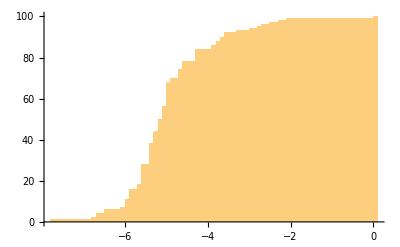

```mathematica
Histogram[Log[Abs[#]]&/@spec,{.1},"CumulativeCount"]
```

```mathematica
hlist=(specAbs=Sort[Log[Abs[#]]&/@spec];Join[{{specAbs_⟦1⟧-1,0}},Transpose[{specAbs,Table[n,{n,1,Length[specAbs]}]}],{{0,Length[specAbs]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-8.79316,0)(-7.79316,1)(-6.75797,2)(-6.61022,3)(-6.61022,4)(-6.47272,5)(-6.47272,6)(-6.0236,7)(-5.96303,8)(-5.96303,9)(-5.9153,10)(-5.9153,11)(-5.83552,12)(-5.83552,13)(-5.81416,14)(-5.81416,15)(-5.80061,16)(-5.64156,17)(-5.64156,18)(-5.58745,19)(-5.564,20)(-5.564,21)(-5.55927,22)(-5.55927,23)(-5.55281,24)(-5.55281,25)(-5.52048,26)(-5.51195,27)(-5.51195,28)(-5.39437,29)(-5.39437,30)(-5.39236,31)(-5.39236,32)(-5.37015,33)(-5.33845,34)(-5.33845,35)(-5.32709,36)(-5.32709,37)(-5.31967,38)(-5.27754,39)(-5.27754,40)(-5.25642,41)(-5.25642,42)(-5.22265,43)(-5.22265,44)(-5.13865,45)(-5.13865,46)(-5.12128,47)(-5.12128,48)(-5.11585,49)(-5.11585,50)(-5.07714,51)(-5.07714,52)(-5.07597,53)(-5.07597,54)(-5.06297,55)(-5.06297,56)(-4.98985,57)(-4.98985,58)(-4.97372,59)(-4.97372,60)(-4.9733,61)(-4.9733,62)(-4.95968,63)(-4.95968,64)(-4.92635,65)(-4.92635,66)(-4.91569,67)(-4.91569,68)(-4.81722,69)(-4.81722,70)(-4.67325,71)(-4.67325,72)(-4.60852,73)(-4.60852,74)(-4.56349,75)(-4.56349,76)(-4.53975,77)(-4.53975,78)(-4.29814,79)(-4.29814,80)(-4.2556,81)(-4.2556,82)(-4.22271,83)(-4.20521,84)(-3.87155,85)(-3.87155,86)(-3.76321,87)(-3.76321,88)(-3.60627,89)(-3.60627,90)(-3.50899,91)(-3.50899,92)(-3.24141,93)(-2.98135,94)(-2.72734,95)(-2.61449,96)(-2.40471,97)(-2.20349,98)(-2.00457,99)(0.,100)(0.,100)

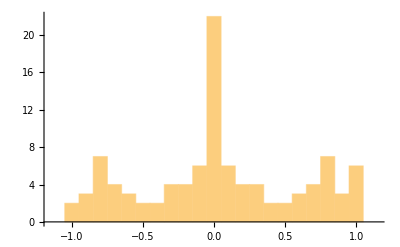

```mathematica
Histogram[Arg[#]/π&/@spec,{-1.15,1.15,.1}]
```

```mathematica
hlist=(specArg=Sort[Arg[#]/π&/@spec];Join[{{-1.15,0}},Transpose[{specArg,Table[n,{n,1,Length[specArg]}]}],{{1.05,Length[specArg]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-1.15,0)(-0.973973,1)(-0.966248,2)(-0.940293,3)(-0.88305,4)(-0.879144,5)(-0.846465,6)(-0.83379,7)(-0.816525,8)(-0.802595,9)(-0.779956,10)(-0.754851,11)(-0.752593,12)(-0.735184,13)(-0.668978,14)(-0.6634,15)(-0.655112,16)(-0.638096,17)(-0.625817,18)(-0.553111,19)(-0.471373,20)(-0.460891,21)(-0.434716,22)(-0.38324,23)(-0.321649,24)(-0.309054,25)(-0.297643,26)(-0.256745,27)(-0.220319,28)(-0.201366,29)(-0.170479,30)(-0.165997,31)(-0.133734,32)(-0.117182,33)(-0.113244,34)(-0.092505,35)(-0.0594225,36)(-0.0502421,37)(-0.0336255,38)(-0.0324377,39)(-0.0085419,40)(-0.00745288,41)(0.,42)(0.,43)(0.,44)(0.,45)(0.,46)(0.,47)(0.,48)(0.,49)(0.,50)(0.,51)(0.,52)(0.,53)(0.,54)(0.,55)(0.00745288,56)(0.0085419,57)(0.0324377,58)(0.0336255,59)(0.0502421,60)(0.0594225,61)(0.092505,62)(0.113244,63)(0.117182,64)(0.133734,65)(0.165997,66)(0.170479,67)(0.201366,68)(0.220319,69)(0.256745,70)(0.297643,71)(0.309054,72)(0.321649,73)(0.38324,74)(0.434716,75)(0.460891,76)(0.471373,77)(0.553111,78)(0.625817,79)(0.638096,80)(0.655112,81)(0.6634,82)(0.668978,83)(0.735184,84)(0.752593,85)(0.754851,86)(0.779956,87)(0.802595,88)(0.816525,89)(0.83379,90)(0.846465,91)(0.879144,92)(0.88305,93)(0.940293,94)(0.966248,95)(0.973973,96)(1.,97)(1.,98)(1.,99)(1.,100)(1.05,100)

#### Preparations for [1, Fig. 4]

```mathematica
P=Pru;
```

```mathematica
rP=#/Max[#]&/@Pru;
```

```mathematica
Export["Pru100.txt",StringRiffle[Table["\\put(0,"<>ToString[50-0.5*(i-1)]<>"){"<>StringJoin[Table[prep=ToExpression[ToString[TempRGB[rP_⟦i,j⟧]]];("\\pxl{"<>ToString[prep_⟦1⟧]<>"}{"<>ToString[prep_⟦2⟧]<>"}{"<>ToString[prep_⟦3⟧]<>"}"),{j,1,100}]]<>"}",{i,1,100}],"\n"]]
```

Pru100.txt

```mathematica
v=Eigenvectors[Transpose[P],1];
```

```mathematica
u=Reverse[Sort[Total[Transpose[#_⟦1⟧]_⟦2⟧]&/@Take[NonStopClustersRussian,100]]]
```

{976,809,642,587,434,410,401,353,338,314,309,303,296,272,265,265,256,250,235,229,223,217,216,215,206,203,198,198,197,195,190,189,189,188,182,179,179,178,177,177,177,171,170,170,167,166,161,160,160,158,157,155,152,151,142,141,141,139,138,136,136,135,134,131,131,130,130,129,129,125,125,124,124,122,122,120,119,118,116,115,114,113,113,113,113,112,112,111,111,111,111,110,109,109,109,109,108,107,105,105}

```mathematica
prep=N[u/Total[u]];StringJoin[Table["("<>ToString[n]<>","<>ToString[prep[[n]]]<>")",{n,1,N0}]]
```

(1,0.0496137)(2,0.0411244)(3,0.0326352)(4,0.0298394)(5,0.0220618)(6,0.0208418)(7,0.0203843)(8,0.0179443)(9,0.0171818)(10,0.0159618)(11,0.0157076)(12,0.0154026)(13,0.0150468)(14,0.0138268)(15,0.0134709)(16,0.0134709)(17,0.0130134)(18,0.0127084)(19,0.0119459)(20,0.0116409)(21,0.0113359)(22,0.0110309)(23,0.0109801)(24,0.0109292)(25,0.0104717)(26,0.0103192)(27,0.0100651)(28,0.0100651)(29,0.0100142)(30,0.00991257)(31,0.0096584)(32,0.00960756)(33,0.00960756)(34,0.00955673)(35,0.00925173)(36,0.00909923)(37,0.00909923)(38,0.00904839)(39,0.00899756)(40,0.00899756)(41,0.00899756)(42,0.00869256)(43,0.00864172)(44,0.00864172)(45,0.00848922)(46,0.00843839)(47,0.00818422)(48,0.00813339)(49,0.00813339)(50,0.00803172)(51,0.00798089)(52,0.00787922)(53,0.00772672)(54,0.00767588)(55,0.00721838)(56,0.00716755)(57,0.00716755)(58,0.00706588)(59,0.00701505)(60,0.00691338)(61,0.00691338)(62,0.00686255)(63,0.00681171)(64,0.00665921)(65,0.00665921)(66,0.00660838)(67,0.00660838)(68,0.00655754)(69,0.00655754)(70,0.00635421)(71,0.00635421)(72,0.00630338)(73,0.00630338)(74,0.00620171)(75,0.00620171)(76,0.00610004)(77,0.00604921)(78,0.00599837)(79,0.00589671)(80,0.00584587)(81,0.00579504)(82,0.0057442)(83,0.0057442)(84,0.0057442)(85,0.0057442)(86,0.00569337)(87,0.00569337)(88,0.00564254)(89,0.00564254)(90,0.00564254)(91,0.00564254)(92,0.0055917)(93,0.00554087)(94,0.00554087)(95,0.00554087)(96,0.00554087)(97,0.00549004)(98,0.0054392)(99,0.00533754)(100,0.00533754)

```mathematica
prep=N[v_⟦1⟧/Total[v_⟦1⟧]];StringJoin[Table["("<>ToString[n]<>","<>ToString[prep[[n]]]<>")",{n,1,N0}]]
```

(1,0.0491085)(2,0.0403593)(3,0.0322514)(4,0.0293017)(5,0.02218)(6,0.0228964)(7,0.0206542)(8,0.0195239)(9,0.0168913)(10,0.0163486)(11,0.0152513)(12,0.0159586)(13,0.0144983)(14,0.0133948)(15,0.01337)(16,0.0140115)(17,0.0129495)(18,0.0123139)(19,0.0116593)(20,0.011704)(21,0.0118923)(22,0.0107301)(23,0.0109083)(24,0.0102978)(25,0.0101363)(26,0.00980707)(27,0.00972002)(28,0.00983933)(29,0.00984534)(30,0.009544)(31,0.00998735)(32,0.0093997)(33,0.0100086)(34,0.0102661)(35,0.00922706)(36,0.00950744)(37,0.0111703)(38,0.00873344)(39,0.00896157)(40,0.00883179)(41,0.00920684)(42,0.00887126)(43,0.00847218)(44,0.00883869)(45,0.00829216)(46,0.00861856)(47,0.008059)(48,0.00796791)(49,0.0080954)(50,0.00782698)(51,0.00773675)(52,0.00882366)(53,0.00761216)(54,0.00754491)(55,0.00694385)(56,0.00713372)(57,0.00703056)(58,0.00690301)(59,0.00701182)(60,0.00687013)(61,0.00747747)(62,0.00695735)(63,0.00679025)(64,0.00633655)(65,0.006369)(66,0.00642344)(67,0.00655515)(68,0.00626369)(69,0.00661002)(70,0.00619594)(71,0.00650981)(72,0.00621363)(73,0.00624334)(74,0.00618517)(75,0.00602107)(76,0.00636366)(77,0.00578167)(78,0.00598319)(79,0.00589539)(80,0.00566456)(81,0.00566568)(82,0.00581031)(83,0.00568159)(84,0.00546077)(85,0.00639339)(86,0.00565813)(87,0.0057607)(88,0.0055139)(89,0.0055663)(90,0.00566745)(91,0.00550983)(92,0.00537504)(93,0.00544992)(94,0.00559342)(95,0.00569189)(96,0.00537574)(97,0.00546561)(98,0.0053419)(99,0.00553853)(100,0.00533959)

```mathematica
1/Total[v_⟦1⟧] Sum[v_⟦1,i⟧*P_⟦i,j⟧,{i,1,N0},{j,1,N0}]
```

1.

```mathematica
StringJoin["("<>ToString[#_⟦1⟧]<>","<>ToString[AccountingForm[#_⟦2⟧]]<>")"&/@Table[M=MatrixPower[P,k];{k,1/2 Sum[Abs[1/Total[v_⟦1⟧] v_⟦1,i⟧*M_⟦i,j⟧-1/Total[v_⟦1⟧] v_⟦1,j⟧*M_⟦j,i⟧],{i,1,N0},{j,1,N0}]},{k,1,5}]]
```

(1,0.06581611214634)(2,0.00385637191009)(3,0.00041145081506)(4,0.0000496887858)(5,0.0000062374825)

### Data for topic patterns

```mathematica
TopicClusters=DeleteCases[NonStopClusters,{_,_,_,"B",_,_,_,_}];
```

```mathematica
Length[TopicClusters]
```

242

```mathematica
SelectedClusters=TopicClusters;
```

```mathematica
TopicClustersRussian=TopicClusters;
```

```mathematica
Timing[PruTopic=Table[Table[prepP=TransitionMeasure[SelectedClusters_⟦m,1⟧,SelectedClusters_⟦n,1⟧,SelectedClusters_⟦m,5⟧,SelectedClusters_⟦m,6⟧],{n,1,Length[SelectedClusters]}],{m,1,Length[SelectedClusters]}];]
```

{176.203,Null}

```mathematica
Timing[PruT=Table[v=Table[prepP=PruTopic_⟦m,n⟧;prepP_⟦1⟧*Exp[-prepP_⟦2⟧],{n,1,100}];v/Total[v],{m,1,100}];]
```

{0.046875,Null}

```mathematica
Timing[spec=Eigenvalues[PruT];]
```

{1.28125,Null}

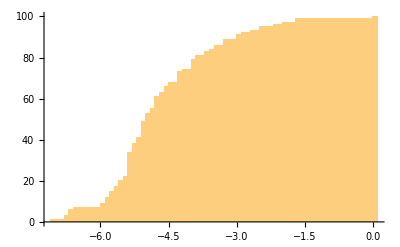

```mathematica
Histogram[Log[Abs[#]]&/@spec,{.1},"CumulativeCount"]
```

```mathematica
hlist=(specAbs=Sort[Log[Abs[#]]&/@spec];Join[{{specAbs_⟦1⟧-1,0}},Transpose[{specAbs,Table[n,{n,1,Length[specAbs]}]}],{{0,Length[specAbs]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-8.08712,0)(-7.08712,1)(-6.7726,2)(-6.7726,3)(-6.68999,4)(-6.68999,5)(-6.65038,6)(-6.56482,7)(-5.94413,8)(-5.94413,9)(-5.8923,10)(-5.8923,11)(-5.85696,12)(-5.76533,13)(-5.76533,14)(-5.76007,15)(-5.61775,16)(-5.61775,17)(-5.59423,18)(-5.53113,19)(-5.53113,20)(-5.44901,21)(-5.44901,22)(-5.3966,23)(-5.3966,24)(-5.39237,25)(-5.39237,26)(-5.3731,27)(-5.3731,28)(-5.35357,29)(-5.35357,30)(-5.32114,31)(-5.32114,32)(-5.30668,33)(-5.30668,34)(-5.2606,35)(-5.2606,36)(-5.24873,37)(-5.24873,38)(-5.19508,39)(-5.19508,40)(-5.10284,41)(-5.09589,42)(-5.09589,43)(-5.04939,44)(-5.04939,45)(-5.02237,46)(-5.02237,47)(-5.02123,48)(-5.02123,49)(-4.98537,50)(-4.95864,51)(-4.95864,52)(-4.95764,53)(-4.89244,54)(-4.89244,55)(-4.79014,56)(-4.79014,57)(-4.77221,58)(-4.77221,59)(-4.74531,60)(-4.74531,61)(-4.61631,62)(-4.61631,63)(-4.59054,64)(-4.59054,65)(-4.53226,66)(-4.43141,67)(-4.43141,68)(-4.29416,69)(-4.27163,70)(-4.27163,71)(-4.24548,72)(-4.24548,73)(-4.10708,74)(-3.96625,75)(-3.96625,76)(-3.9587,77)(-3.91282,78)(-3.91282,79)(-3.81688,80)(-3.81688,81)(-3.64019,82)(-3.64019,83)(-3.5956,84)(-3.46345,85)(-3.46345,86)(-3.26268,87)(-3.26268,88)(-3.20026,89)(-2.96505,90)(-2.96505,91)(-2.8086,92)(-2.68018,93)(-2.4459,94)(-2.4459,95)(-2.12939,96)(-1.99014,97)(-1.69147,98)(-1.69147,99)(0.,100)(0.,100)

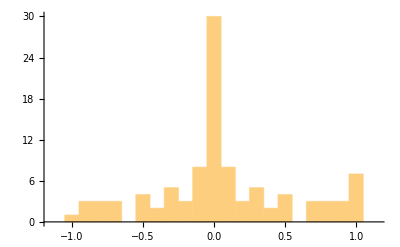

```mathematica
Histogram[Arg[#]/π&/@spec,{-1.15,1.15,.1}]
```

```mathematica
hlist=(specArg=Sort[Arg[#]/π&/@spec];Join[{{-1.15,0}},Transpose[{specArg,Table[n,{n,1,Length[specArg]}]}],{{1.05,Length[specArg]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-1.15,0)(-0.955344,1)(-0.920276,2)(-0.887241,3)(-0.885208,4)(-0.821096,5)(-0.797373,6)(-0.757588,7)(-0.724567,8)(-0.716455,9)(-0.691193,10)(-0.53251,11)(-0.492255,12)(-0.491962,13)(-0.474121,14)(-0.42707,15)(-0.366383,16)(-0.337839,17)(-0.325297,18)(-0.29605,19)(-0.294931,20)(-0.258125,21)(-0.231772,22)(-0.217066,23)(-0.179788,24)(-0.145358,25)(-0.143072,26)(-0.131285,27)(-0.125166,28)(-0.114295,29)(-0.10172,30)(-0.064051,31)(-0.0559602,32)(-0.0388223,33)(-0.0274448,34)(-0.023804,35)(-0.0217014,36)(-0.0202792,37)(-0.0149351,38)(-0.00440476,39)(-0.000440537,40)(0.,41)(0.,42)(0.,43)(0.,44)(0.,45)(0.,46)(0.,47)(0.,48)(0.,49)(0.,50)(0.,51)(0.,52)(0.,53)(0.,54)(0.000440537,55)(0.00440476,56)(0.0149351,57)(0.0202792,58)(0.0217014,59)(0.023804,60)(0.0274448,61)(0.0388223,62)(0.0559602,63)(0.064051,64)(0.10172,65)(0.114295,66)(0.125166,67)(0.131285,68)(0.143072,69)(0.145358,70)(0.179788,71)(0.217066,72)(0.231772,73)(0.258125,74)(0.294931,75)(0.29605,76)(0.325297,77)(0.337839,78)(0.366383,79)(0.42707,80)(0.474121,81)(0.491962,82)(0.492255,83)(0.53251,84)(0.691193,85)(0.716455,86)(0.724567,87)(0.757588,88)(0.797373,89)(0.821096,90)(0.885208,91)(0.887241,92)(0.920276,93)(0.955344,94)(1.,95)(1.,96)(1.,97)(1.,98)(1.,99)(1.,100)(1.05,100)

### Preparations for [1, Fig. 5b]

```mathematica
SelectedTopics=Cases[TopicClustersRussian,{{___,{#,_},___},___}]_⟦1⟧&/@TopicsNamesRussian;
```

```mathematica
KinSpecSWLongTag[TopicClustersRussian,PruTopic,#_⟦1⟧&/@SelectedTopics]
```

Here are the lists of eigenvalues for the three selected topics:

```mathematica
RussianKinQ0=KinQ0
```

{{0.97783291929213,0.19978021534072,0.12671156044158,0.089510169546956,0.058335357120577,0.050535691750551,0.050535691750551,0.030991657686771,0.030991657686771,0.028475461740544,0.028475461740544,0.024520000545834,0.022227211408687,0.022227211408687,0.015723287187217,0.014868466465456,0.014868466465456,0.013965274615391,0.013965274615391,0.0097827197857007,0.0097827197857007,0.0080962851378431,0.0072217056504158,0.0042898722378412,0.0027354038412425,0.0013666864642786,0},{0.87855719943367,0.11932387346206,0.064891580927392,0.051789023755835,0.043777758143678,0.040133086049436,0.040133086049436,0.034273094995215,0.029471187633117,0.029471187633117,0.023217345765747,0.022271963580166,0.020846123215198,0.020846123215198,0.016194031035541,0.016194031035541,0.0118721921076,0.0118721921076,0.010033210918804,0.010033210918804,0.009883413322986,0.0087692432108478,0.0087692432108478,0.008473340184075,0.008473340184075,0.0071897514930348,0.0071897514930348,0.0068785457117455,0.0068785457117455,0.0054626729328574,0.0054626729328574,0.0039406055145958,0.0039406055145958,0.0020683082915577,0.0020683082915577,0.0019719949036467,0.0019719949036467,0},{0.76973134597875,0.1512330309057,0.13624635840089,0.086921697032741,0.047671804349637,0.04141341399241,0.026413320776426,0.026413320776426,0.022663347181435,0.022663347181435,0.015992835383032,0.01247856084481,0.01247856084481,0.011098552590993,0.011098552590993,0.0096962028432808,0.0096962028432808,0.0064669941379363,0.0063668941873461,0.0063668941873461,0.0061735629928942,0.0061735629928942,0.0057280225284835,0.0057280225284835,0.0056755509475102,0.0056755509475102,0.0053505073380256,0.0053505073380256,0.0034517876547614,0.0034517876547614,0.0024399030511339,0.0024399030511339,0}}

```mathematica
RussianKinQ=KinQ
```

{{0.97783291929213,0.19978021534072,0.12671156044158,0.089510169546956,0.058335357120577,0.050535691750551,0.050535691750551,0.030991657686771,0.030991657686771,0.028475461740544,0.028475461740544,0.024520000545834,0.022227211408687,0.022227211408687,0.015723287187217},{0.87855719943367,0.11932387346206,0.064891580927392,0.051789023755835,0.043777758143678,0.040133086049436,0.040133086049436,0.034273094995215,0.029471187633117,0.029471187633117,0.023217345765747,0.022271963580166,0.020846123215198,0.020846123215198,0.016194031035541,0.016194031035541,0.0118721921076},{0.76973134597875,0.1512330309057,0.13624635840089,0.086921697032741,0.047671804349637,0.04141341399241,0.026413320776426,0.026413320776426,0.022663347181435,0.022663347181435,0.015992835383032,0.01247856084481,0.01247856084481,0.011098552590993}}

```mathematica
TopicNames=TopicsNamesRussian
```

{гордость,дарси,элизабет}

```mathematica
Cl=TopicClustersRussian;
```

```mathematica
PT=PruTopic;
```

```mathematica
AffinitySmallWorlds=Table[PT_⟦SeekPos[TopicNames_⟦k⟧,Cl],TopicSmallWorlds_⟦k,j⟧,3⟧,{k,1,Length[TopicNames]},{j,1,Length[TopicSmallWorlds_⟦k⟧]}];
```

```mathematica
SmallWorldWeights=Table[v=Eigenvectors[Transpose[RenormPSW_⟦k⟧],1];prob=v_⟦1⟧/Total[v_⟦1⟧];Table[ReplacePart[Cl_⟦TopicSmallWorlds_⟦k,m⟧⟧,{2->prob_⟦m⟧,5->AffinitySmallWorlds_⟦k,m⟧}],{m,1,Length[RenormPSW_⟦k⟧]}],{k,1,Length[RenormPSW]}];
```

```mathematica
SortWordClusters[list_,ScalingFactor_,MaxClusters_]:=(AllCluster=Take[Sort[(prep=CensorCluster[#_⟦1⟧];{prep,#_⟦2⟧,Total[Transpose[prep]_⟦2⟧],#_⟦4⟧,#_⟦5⟧})&/@list,#1[[2]]>#2[[2]]&],UpTo[MaxClusters]];SizedWords=Table[Width=Total[Max/@StringLength[#_⟦2⟧&/@#&/@SplitEven[EvenOut[Transpose[AllCluster_⟦n,1⟧]]]]];ScalingFactor √(AllCluster_⟦n,2⟧/Width)*{Width*0.95,1/0.9},{n,1,Length[AllCluster]}];)
```

```mathematica
SmallWorldCloudPlot[ScalingFactor_,MaxClusters_,OutputFileName_]:=(FindCenter[SizedWords];MinX=Min[Table[CenterList_⟦n,1⟧-SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MinY=Min[Table[CenterList_⟦n,2⟧-SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];MaxX=Max[Table[CenterList_⟦n,1⟧+SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MaxY=Max[Table[CenterList_⟦n,2⟧+SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];ArrangedCluster=Table[WCCounts=Transpose[SortBy[AllCluster_⟦n,1⟧,First]];{SizedWords_⟦n⟧,WCCounts_⟦1⟧,WCCounts_⟦2⟧,AllCluster_⟦n,3⟧,AllCluster_⟦n,4⟧,CenterList_⟦n⟧,AllCluster_⟦n,5⟧},{n,1,Length[AllCluster]}];Export[OutputFileName,"\\begin{minipage}{\\textwidth}\\fontfamily{ptm}\\selectfont\\begin{spacing}{0}\\begin{picture}("<>ToString[N[Round[MaxX-MinX,10^-3]]]<>","<>ToString[N[Round[MaxY-MinY,10^-3]]]<>"){\\textbf{"<>StringJoin[Table["\\put("<>ToString[N[Round[ArrangedCluster_⟦k,6,1⟧-ArrangedCluster_⟦k,1,1⟧/2,10^-3]]]<>","<>ToString[N[Round[ArrangedCluster_⟦k,6,2⟧-ArrangedCluster_⟦k,1,2⟧/2,10^-3]]]<>"){\\textcolor[rgb]"<>ToString[RainbowRGB[ArrangedCluster_⟦k,7⟧]]<>"{"<>"
\\setlength{\\unitlength}{"<>ToString[N[Round[0.85*2.54/72 ArrangedCluster_⟦k,1,2⟧,10^-3]]]<>"cm}{
"<>(BCData=Word2BarChart[{ArrangedCluster_⟦k,2⟧,ArrangedCluster_⟦k,3⟧}];H=ArrangedCluster_⟦k,4⟧;StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[(BCData_⟦m,n,2⟧==" ")||(BCData_⟦m,n,3⟧/H*0.85 ArrangedCluster_⟦k,1,2⟧*2.54/72<0.01),"","\\BC{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>(temp=ToUpperCase[BCData_⟦m,n,2⟧];ToString[N[Round[BCData_⟦m,n,3⟧/H*If[StringContainsQ[temp,"Й"],1.4,1],10^-3]]])<>"}{\\ru{"<>StringReplace[temp,{"ТС":>"Т{}С","КХ":>"К{}Х"}]<>"}}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}}
",{k,1,Length[ArrangedCluster]}]]<>"}}\\end{picture}\\end{spacing}\\end{minipage}"];Close[str];)
```

```mathematica
SortWordClusters[SmallWorldWeights_⟦1⟧,30,Length[SmallWorldWeights_⟦1⟧]];SmallWorldCloudPlot[1,20,"ru-pride.txt"];
```

```mathematica
SortWordClusters[SmallWorldWeights_⟦2⟧,30,Length[SmallWorldWeights_⟦2⟧]];SmallWorldCloudPlot[1,25,"ru-Darcy.txt"];
```

```mathematica
SortWordClusters[SmallWorldWeights_⟦3⟧,30,Length[SmallWorldWeights_⟦3⟧]];SmallWorldCloudPlot[1,25,"ru-Eliza.txt"];
```

### Word translation

#### Bulk vectors

```mathematica
EnglishRef=TopicClustersEnglish;
```

```mathematica
RussianRef=TopicClustersRussian;
```

```mathematica
PandPChapEnglish=StringSplit[ExampleData[{"Text","PrideAndPrejudice"}],"Chapter "~~DigitCharacter..~~" "];
```

```mathematica
Length[PandPChapEnglish]
```

61

```mathematica
VecEnglish=Table[{EnglishRef_⟦k,1⟧,StringCount[PandPChapEnglish,WordBoundary~~Alternatives@@(#_⟦1⟧&/@EnglishRef_⟦k,1⟧)~~WordBoundary,IgnoreCase->True]},{k,1,Length[EnglishRef]}];
```

```mathematica
PandPChapRussian=StringSplit[StringReplace[ImportString[StringReplace[StringReplace[StringReplace[StringReplace[CleanseText[Import["Гордость_и_предубеждение.txt"]],"\n":>"\n舜"],{(s:("舜"~~Repeated[Except["\n"],{2,75}]))~~"\n":>s<>"垚"}],"":>""],{"舜":>""}],"HTML"],{"垚":>"\n\n"}],"ГЛАВА"~~" "..~~("I"|"V"|"X"|"Х"|"L")..];
```

```mathematica
Length[PandPChapRussian]
```

61

```mathematica
VecRussian=Table[{RussianRef_⟦k,1⟧,StringCount[PandPChapRussian,WordBoundary~~Alternatives@@(#_⟦1⟧&/@RussianRef_⟦k,1⟧)~~WordBoundary,IgnoreCase->True]},{k,1,Length[RussianRef]}];
```

```mathematica
FlatScreenedPairs=Flatten[Table[{#_⟦1⟧,#_⟦2,k⟧},{k,1,Length[#_⟦2⟧]}]&/@Select[Table[{EnglishRef[[k,1]],#_⟦1⟧&/@Select[VecRussian,JaccardRuzickaSim[#_⟦2⟧,Cases[VecEnglish,{EnglishRef[[k,1]],___}]_⟦1,2⟧]≥Max[1-7/100*√61,1-√(Length[Select[Min[#]&/@Transpose[{#_⟦2⟧,Cases[VecEnglish,{EnglishRef[[k,1]],___}]_⟦1,2⟧}],#>0&]]/Total[Max[#]&/@Transpose[{#_⟦2⟧,Cases[VecEnglish,{EnglishRef[[k,1]],___}]_⟦1,2⟧}]])]&]},{k,1,Length[EnglishRef]}],Length[#_⟦2⟧]>0&],1];
```

```mathematica
SiftedTags=Union[(#_⟦1⟧&/@FlatScreenedPairs)];SiftedEnglishRef=Reverse[SortBy[Table[Cases[EnglishRef,{SiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[SiftedTags]}],#_⟦3⟧&]];
```

```mathematica
SiftedTags=Union[(#_⟦2⟧&/@FlatScreenedPairs)];SiftedRussianRef=Reverse[SortBy[Table[Cases[RussianRef,{SiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[SiftedTags]}],#_⟦3⟧&]];
```

```mathematica
Length[SiftedEnglishRef]
```

84

```mathematica
Length[SiftedRussianRef]
```

83

#### Spectral parameters for English

```mathematica
FromTopics=SiftedEnglishRef;
```

```mathematica
FromDelta=ReadDelta[#]&/@FromTopics;
```

```mathematica
FromN=(#_⟦3⟧-1)&/@FromTopics;
```

```mathematica
AbsoluteTiming[KinSpecSWLongTag[TopicClustersEnglish,PenTopic,#_⟦1⟧&/@FromTopics];]
```

{48.3134,Null}

```mathematica
FromKinQ=KinQ;
```

```mathematica
FromEta=SemanticComplexities;
```

#### Spectral parameters for Russian

```mathematica
ToTopicsRussian=SiftedRussianRef;
```

```mathematica
Length[ToTopicsRussian]
```

83

```mathematica
ToDeltaRussian=ReadDelta[#]&/@ToTopicsRussian;
```

```mathematica
ToNRussian=(#_⟦3⟧-1)&/@ToTopicsRussian;
```

```mathematica
AbsoluteTiming[KinSpecSWLongTag[TopicClustersRussian,PruTopic,#_⟦1⟧&/@ToTopicsRussian];]
```

{86.5256,Null}

```mathematica
ToKinRussian=KinQ;
```

```mathematica
ToEtaRussian=SemanticComplexities;
```

#### Translation

```mathematica
AbsoluteTiming[fromLabeled=Transpose[{#_⟦1⟧&/@FromTopics,FromKinQ}];toLabeled=Transpose[{#_⟦1⟧&/@ToTopicsRussian,ToKinRussian}];Report=Table[{FlatScreenedPairs_⟦k⟧,(JaccardRuzickaSim[Cases[fromLabeled,{FlatScreenedPairs_⟦k,1⟧,_}]_⟦1,2⟧,Cases[toLabeled,{FlatScreenedPairs_⟦k,2⟧,_}]_⟦1,2⟧])},{k,1,Length[FlatScreenedPairs]}];]
```

{0.0139779,Null}

```mathematica
prep=Union[Select[Table[{Report_⟦n,1,1⟧,Report_⟦n,1,2⟧,Report_⟦n,2⟧},{n,1,Length[Report]}],#_⟦3⟧≥0.7&]];g=Graph[(#_⟦1⟧->#_⟦2⟧)&/@prep,EdgeWeight->(#_⟦3⟧&/@prep)];(KuhnSln={#,FindRowRank[#,prep],FindColRank[#,prep]}&/@Select[{#,PropertyValue[{g,#},EdgeWeight]}&/@FindIndependentEdgeSet[g],#_⟦2⟧>0&])//TableForm
```

{{Brighton,24}}->{{брайтон,17},{брайтона,4},{брайтоне,5}}
0.84666979543965 | 1 | 1
{{de,39}}->{{бур,40},{буром,1},{бура,3},{буря,2},{бурном,1},{бурна,1},{бурю,2}}
0.85750990282249 | 1 | 1
{{Bourgh,35},{Bourgh's,4}}->{{де,46}}
0.81567284323523 | 2 | 2
{{Derbyshire,24}}->{{дербишир,4},{дербиширом,1},{дербишира,9},{дербишире,12}}
0.81580465999414 | 1 | 1
{{five,30}}->{{пятам,1},{пятом,1},{пяти,9},{пять,20},{пятью,1},{пятницу,1},{пятую,1},{пятна,2}}
0.78157894439396 | 1 | 1
{{library,23}}->{{библиотека,2},{библиотеке,7},{библиотеки,5},{библиотекой,2},{библиотеку,7}}
0.89943498262514 | 1 | 1
{{London,55}}->{{лондон,42},{лондона,16},{лондоне,25},{лондону,1}}
0.86052031139841 | 1 | 1
{{Meryton,57}}->{{мер,1},{мери,1},{меритон,18},{меритоном,1},{меритона,9},{меритоне,24},{меритону,3}}
0.85698304288423 | 1 | 1
{{money,26}}->{{денег,13},{денежных,2},{денежные,3},{деньгам,2},{деньгах,1},{деньгами,2},{деньги,5}}
0.81186518644219 | 1 | 1
{{Mr,786}}->{{мистер,471},{мистером,77},{мистера,320},{мистере,23},{мистеру,85}}
0.79180344937007 | 1 | 1
{{Mrs,343}}->{{миссис,401}}
0.92467674278057 | 1 | 1
{{Netherfield,73}}->{{незерфилд,26},{незерфилдом,3},{незерфилда,11},{незерфилде,37},{незерфилду,2}}
0.90728457516975 | 1 | 1
{{park,22}}->{{парк,12},{парков,1},{парка,10},{парке,1},{парковую,1},{парку,4}}
0.86168691463356 | 1 | 1
{{Pemberley,53}}->{{пемберли,55}}
0.85188026202691 | 1 | 1
{{pounds,24}}->{{тысяч,15},{тысячам,1},{тысячах,2},{тысяча,3},{тысячами,3},{тысячи,7},{тысячу,1}}
0.75406419228014 | 2 | 2
{{thousand,34}}->{{фунтов,23}}
0.86249876755158 | 1 | 1
{{Rosings,49}}->{{розингс,15},{розингсом,3},{розингса,13},{розингсе,18},{розингских,1},{розингсу,1},{врозингсе,1}}
0.87825316517179 | 1 | 1
{{sir,78}}->{{сэр,58},{сэром,5},{сэра,16},{сэру,3}}
0.86735979856549 | 2 | 1
{{William,40},{William's,6}}->{{уильям,26},{уильямом,4},{уильяма,13},{уильяму,3}}
0.91142082450563 | 1 | 1
{{ball,34},{balls,8}}->{{бал,19},{балов,1},{балом,2},{бала,14},{балами,1},{бале,4},{бальных,1},{бальный,1},{балу,14},{балы,6}}
0.86423521242059 | 1 | 1
{{Catherine,110},{Catherine's,16}}->{{леди,182}}
0.90230104427986 | 1 | 1
{{Charlotte,68},{Charlotte's,17}}->{{шарлотте,8},{шарлотта,61},{шарлоттой,9},{шарлотту,5},{шарлотты,19}}
0.93226654421404 | 1 | 1
{{civilities,7},{civility,42}}->{{любезен,5},{любезного,1},{любезностях,1},{любезна,1},{любезностями,1},{любезная,1},{любезнее,1},{любезнейшим,2},{любезности,10},{любезно,15},{любезной,2},{любезность,10},{любезное,4},{любезностью,4},{любезные,2},{любезным,9}}
0.86854034703852 | 1 | 1
{{Collins,156},{Collins's,24}}->{{коллинз,123},{коллинзов,4},{коллинзом,11},{коллинза,64},{коллинзами,1},{коллинзе,2},{коллинзу,12},{коллинзы,6}}
0.82048660621534 | 1 | 1
{{colonel,65},{colonel's,1}}->{{полковник,35},{полкового,2},{полковником,6},{полковника,16},{полковнику,10}}
0.74777895915596 | 1 | 1
{{Darcy,374},{Darcy's,44}}->{{дарси,587}}
0.8874759975517 | 1 | 1
{{dinner,33},{dinners,2}}->{{обед,16},{обедом,4},{обеда,12},{обедают,3},{обедаем,1},{обедать,8},{обеду,10},{обеды,3},{обедал,1},{обедала,2},{обедали,5},{обеденным,1}}
0.86772784836482 | 1 | 1
{{father,116},{father's,19}}->{{отца,41},{отце,1},{отцом,9},{отцу,9},{отцы,2},{отец,49},{папа,14},{папе,2},{папы,1},{папой,2},{отцов,1}}
0.92860450355094 | 1 | 1
{{four,33},{four-and-twenty,1}}->{{четыре,22}}
0.73287034711562 | 1 | 1
{{Jane,263},{Jane's,28}}->{{джейн,353}}
0.9080891997791 | 1 | 1
{{Kitty,69},{Kitty's,2}}->{{китти,74}}
0.93574858257707 | 1 | 1
{{Lizzy,95},{Lizzy's,2}}->{{лиззи,95}}
0.9272137297418 | 1 | 1
{{Lydia,133},{Lydia's,38}}->{{лидия,93},{лидией,11},{лидии,74},{лидию,11}}
0.87953021237849 | 1 | 1
{{ma'am,7},{madam,21}}->{{сударыня,26}}
0.88055633404395 | 1 | 1
{{Mary,38},{Mary's,1}}->{{мэром,1},{мэри,38}}
0.90912376375935 | 1 | 1
{{regiment,19},{regiment's,3}}->{{полк,20},{полком,2},{полка,9},{полке,1},{полку,7}}
0.85360793215382 | 1 | 1
{{room,112},{rooms,8}}->{{каменное,1},{камней,1},{комнат,1},{комнатам,2},{комнатах,2},{комната,4},{комнате,32},{комнатой,3},{комнату,39},{комнаты,19}}
0.89417440143594 | 1 | 1
{{table,28},{tables,3}}->{{стол,10},{столом,14},{стола,7},{столик,2},{столика,1},{столике,1},{столице,4},{столику,1},{столицу,2},{столицы,1},{столовая,1},{столовой,3},{столовую,7},{столу,6},{столы,4}}
0.72821367995569 | 1 | 1
{{ten,33},{tens,1}}->{{десятка,1},{десяти,9},{десятину,1},{десять,18},{десятью,1},{десятков,1}}
0.89221986887751 | 1 | 1
{{week,29},{weeks,18}}->{{неделя,5},{неделе,2},{недели,28},{недель,13},{недельку,1},{неделю,18}}
0.87007447977115 | 1 | 1
{{Wickham,162},{Wickham's,32}}->{{уикхему,18},{уикхем,91},{уикхемам,1},{уикхемов,1},{уикхемом,32},{уикхема,86},{уикхеме,19},{уикхемы,2}}
0.80907914346241 | 1 | 1
{{window,16},{windows,6}}->{{оклик,1},{окном,1},{окна,14},{окнами,2},{окне,1},{окно,2},{окон,4},{окну,4}}
0.89166551694784 | 1 | 1
{{aunt,78},{aunt's,6},{aunts,1}}->{{тетка,10},{тетя,11},{тетушка,14},{тетушке,4},{тетушки,6},{тетушкины,1},{тетушкой,2},{тетушку,2},{тетей,3},{тетке,7},{тети,4},{тетки,8},{теткой,3},{тетку,1},{тетю,1}}
0.86965031981143 | 1 | 1
{{beautiful,15},{beauties,4},{beauty,27}}->{{краска,1},{красавцев,1},{красавица,2},{красоте,4},{красота,2},{красотка,1},{красотами,1},{красотой,4},{красоткой,1},{красоту,2},{красоты,9},{краску,2},{красавицам,1},{красавицей,2},{красавицу,1},{красавицы,1},{красило,1},{красивом,1},{красивых,3},{красивого,1},{красива,3},{красивая,2},{красиво,2},{красивой,6},{красивое,1},{красивы,1},{красивый,1},{красивыми,2},{красивые,1},{красивым,3}}
0.89996965494664 | 1 | 1
{{Bennet,294},{Bennet's,29},{Bennets,10}}->{{беннет,372},{беннетам,1},{беннетов,7},{беннетом,6},{беннета,34},{беннету,11},{беннеты,3}}
0.92359563805515 | 1 | 1
{{book,16},{books,13},{book-room,1}}->{{книг,6},{книгах,5},{книга,2},{книге,1},{книги,9},{книгой,2},{книгу,7},{книжки,1}}
0.83616881464134 | 1 | 1
{{child,14},{children,25},{childhood,1}}->{{детям,2},{детства,4},{детей,11},{дети,7},{детьми,5},{ребенка,1},{ребенком,2},{дитя,6}}
0.91921814167373 | 1 | 1
{{cousin,41},{cousin's,8},{cousins,11}}->{{кузен,10},{кузена,15},{кузене,1},{кузену,3},{кузин,7},{кузинам,2},{кузина,9},{кузине,4},{кузиной,3},{кузину,4},{кузины,7}}
0.9342602523235 | 1 | 1
{{dear,158},{dearly,3},{dearest,17}}->{{дорог,1},{дорого,2},{дорогам,1},{дорогих,4},{дорогом,2},{дорогого,2},{дорога,2},{дорогая,74},{дороге,10},{дороги,8},{дорогим,4},{дорогой,44},{дорогу,6},{дорогую,2},{дорожит,2},{дорожкам,2},{дороже,2},{дорожке,6},{дорожки,2},{дорожишь,1},{дорожил,2},{дорожить,2},{дорожила,2},{дорожили,1},{дорожные,2},{дорожкой,1},{дорожу,2},{дорожку,1}}
0.81058316876778 | 1 | 1
{{Eliza,22},{Elizabeth,597},{Elizabeth's,38}}->{{элиза,22},{элизабет,785},{элизе,1},{элизой,1}}
0.83845284904781 | 1 | 1
{{evening,72},{evening's,2},{evenings,4}}->{{вечер,37},{вечеров,1},{вечером,16},{вечера,26},{вечере,2},{вечеринках,1},{вечеринок,1},{вечерних,1},{вечернего,1},{вечерней,2},{вечерние,1},{вечернюю,1},{вечеру,2}}
0.82406715100306 | 1 | 1
{{Forster,38},{Forster's,1},{Forsters,1}}->{{форстер,24},{форстеров,2},{форстером,2},{форстера,6},{форстеру,5},{форстеры,1}}
0.85230081118765 | 1 | 1
{{Gardiner,84},{Gardiner's,13},{Gardiners,6}}->{{гардинер,91},{гардинерам,1},{гардинеров,10},{гардинером,6},{гардинера,15},{гардинерами,2},{гардинеру,4},{гардинеры,7}}
0.89084683690981 | 1 | 1
{{husband,42},{husband's,8},{husbands,4}}->{{муж,10},{мужа,24},{мужей,1},{мужественно,1},{мужем,10},{мужу,9}}
0.89806982652664 | 1 | 1
{{letter,115},{letters,16},{letter-paper,1}}->{{письмам,1},{письмах,1},{письмом,5},{письма,43},{письме,16},{писем,8},{письмо,112},{письму,3}}
0.79879501455653 | 1 | 1
{{man,145},{man's,5},{men,33}}->{{молод,1},{младших,8},{молодом,6},{молодых,23},{младшего,1},{младшему,1},{молодого,20},{молодому,3},{молода,3},{младшая,8},{молодая,6},{младшей,3},{младшим,5},{молодой,33},{молодостью,1},{младшую,1},{молодую,2},{молодыми,5},{молодые,22},{молодым,18},{молоденькой,1},{младший,3},{младшими,4},{молодости,3},{младшие,14}}
0.7851856307054 | 1 | 1
{{maternal,2},{mother,110},{mother's,25}}->{{мама,16},{маме,5},{мамы,1},{мать,41},{матерей,1},{матери,45},{материала,1},{матерью,10}}
0.93128100583549 | 1 | 1
{{Phillip's,1},{Phillips,26},{Phillips's,5}}->{{филипс,30},{филипсам,2},{филипса,6}}
0.88743909896141 | 1 | 1
{{sat,38},{sit,15},{sitting,20}}->{{сел,2},{сесть,4},{сидит,1},{сидеть,3},{уселся,2},{села,3},{уселась,5},{сидя,4},{сидящего,1},{сидел,1},{посидел,1},{сидела,9},{сидели,3},{селений,1},{селение,2},{сидевшая,2},{сидевших,1},{сидевшую,1},{сидевшего,2},{сели,2},{садясь,1},{сидишь,1},{уселись,3},{садилась,1}}
0.79547434569778 | 1 | 1
{{uncle,59},{uncle's,9},{uncles,3}}->{{дядя,19},{дядюшка,3},{дядюшке,2},{дядюшки,9},{дядюшкой,1},{дядюшку,1},{дяде,7},{дядей,4},{дяди,10},{дядины,1},{дядю,5}}
0.81118863363897 | 1 | 1
{{year,28},{years,33},{years',2}}->{{год,13},{лет,33},{лета,2},{годам,1},{года,16},{годами,4},{годовых,2},{годового,3},{году,5},{годы,8}}
0.90513939941312 | 1 | 1
{{Bingley,257},{Bingley's,49},{Bingleys,4},{Bingleys',1}}->{{бингли,410}}
0.86779824582228 | 1 | 1
{{brother,62},{brotherly,2},{brother's,13},{brothers,2}}->{{брат,23},{брата,21},{брате,1},{брату,4},{братом,8},{братья,1},{братьев,2}}
0.91853765251008 | 1 | 1
{{character,64},{characters,3},{characteristic,2},{characterise,1}}->{{характер,31},{характерах,2},{характеров,1},{характером,1},{характера,14},{характере,12},{характеристикой,1},{характеру,4},{характеры,3},{характерным,1}}
0.79803475906294 | 1 | 1
{{daily,3},{day,130},{day's,4},{days,30}}->{{дном,2},{днях,8},{дня,43},{дней,20},{днем,4},{дни,12},{день,69},{ежедневно,6},{ежедневным,1},{каждодневных,1},{дню,4}}
0.77185744940463 | 1 | 1
{{dance,31},{danced,12},{dances,10},{dancing,21}}->{{танец,7},{танцам,4},{танцах,4},{танца,4},{танцами,1},{танце,5},{танцев,5},{танцевал,9},{танцевала,1},{танцевали,2},{танцевальными,1},{танцы,6},{танцевавших,1},{танцевать,26},{танцует,1},{танцуете,5},{танцующих,5},{танцующим,1}}
0.79595637687829 | 1 | 1
{{daughter,78},{daughter's,7},{daughters,49},{daughters',1}}->{{дочь,33},{дочек,6},{дочкам,1},{дочках,1},{дочерям,3},{дочка,7},{дочками,2},{дочке,2},{дочерей,32},{дочки,9},{дочери,48},{дочерьми,3},{дочерью,8}}
0.92518175033957 | 1 | 1
{{dislike,23},{disliked,4},{dislikes,1},{disliking,1}}->{{неприязни,4},{неприязнь,18},{неприязнью,4}}
0.85665839338125 | 1 | 1
{{Lucas,65},{Lucas's,5},{Lucases,13},{Lucases',1}}->{{лукас,69},{лукасам,1},{лукасов,6},{лукаса,5},{лукасами,1},{лукасы,2}}
0.87554806066776 | 1 | 1
{{said,401},{say,160},{saying,35},{says,15}}->{{скажет,4},{скажут,1},{говорит,12},{говорят,2},{говорить,34},{говорится,2},{говоря,34},{сказал,98},{сказала,153},{сказалась,1},{сказали,13},{сказалось,1},{сказанных,2},{сказанного,1},{сказанному,1},{сказанная,1},{сказанное,2},{сказанный,1},{сказанные,1},{сказано,9},{сказаны,1},{сказав,15},{говорящее,1},{скажете,4},{скажешь,4},{скажем,2},{скажи,5},{говори,3},{скажите,9},{говорите,8},{говоришь,1},{говорил,24},{говорила,29},{говорили,11},{говорилось,13},{разговаривает,2},{разговаривая,3},{разговаривал,8},{разговаривала,2},{разговаривали,5},{разговаривать,22},{говоривший,1},{говорившего,2},{сказать,75},{скажу,4},{говорю,9},{сказывается,1},{наговорит,1},{наговориться,3},{наговорил,1}}
0.76752694945004 | 1 | 1
{{vanish,1},{vanished,2},{vain,20},{vanity,18}}->{{тщеславия,3},{тщеславие,12},{тщеславии,2},{тщеславная,1},{тщеславной,1},{тщеславны,1},{тщеславным,2}}
0.81985597576787 | 1 | 1
{{carriage,44},{carriages,6},{carried,8},{carry,5},{carrying,4}}->{{экипаж,20},{экипажах,1},{экипажа,11},{экипаже,5},{экипажей,4},{экипажем,1},{экипажу,4}}
0.90662831647503 | 1 | 1
{{happily,5},{happiness,72},{happy,83},{happier,3},{happiest,10}}->{{счастье,29},{счастья,26},{счастлив,9},{счастливее,2},{счастливое,4},{счастливую,8},{счастливым,11},{счастливых,2},{счастливого,2},{счастливому,1},{посчастливится,1},{счастьем,2},{счастью,12},{счастлива,16},{счастливая,2},{счастливо,3},{счастливой,13},{счастливицей,1},{посчастливилось,10},{счастливейшей,1},{счастливейшим,4},{счастливы,3},{счастливый,4},{счастливыми,2},{счастливые,3}}
0.88450754685667 | 1 | 1
{{miss,283},{missed,3},{missing,1},{missent,2},{missish,1}}->{{мисс,303}}
0.82946007450297 | 1 | 1
{{pride,47},{prided,1},{proud,22},{proudly,1},{proudest,1}}->{{горд,3},{гордом,1},{гордится,2},{горда,3},{гордецом,2},{гордости,8},{гордитесь,1},{гордившаяся,1},{гордо,1},{гордость,25},{гордостью,4},{гордый,1},{гордым,4},{гордилась,2}}
0.93543653446914 | 1 | 1
{{woman,55},{womanly,1},{woman's,4},{women,19},{women's,1}}->{{женщин,16},{женщинам,2},{женщина,17},{женщинами,1},{женщине,5},{женщиной,12},{женщину,2},{женщины,11},{жены,10}}
0.85882108855329 | 1 | 1
{{marriage,66},{married,61},{marry,42},{marrying,23},{matrimonial,1},{matrimony,6}}->{{женаты,1},{женатый,1},{женатым,1},{женат,1},{жених,1},{замуж,48},{женить,3},{женится,6},{поженятся,4},{замужеством,3},{замужества,8},{замужестве,3},{замужем,6},{замужество,8},{женись,1},{жениться,19},{пожениться,1},{свадебных,4},{свадебному,1},{свадебной,2},{свадебное,1},{свадебным,2},{замужних,1},{замужняя,1},{замужней,3},{замужние,1},{свадьба,2},{свадьбе,5},{свадьбой,1},{свадьбу,2},{женился,10},{поженили,2},{поженились,4},{женитьба,8},{женитьбе,4},{женитьбой,3},{женитьбу,7}}
0.93610235853928 | 1 | 1
{{office,6},{officer,8},{officers,29},{officers',2},{officiousness,1},{officious,3}}->{{офицер,6},{офицерам,2},{офицерах,1},{офицеров,16},{офицером,1},{офицерами,8},{офицеры,9},{обофицерах,1}}
0.78963785114134 | 1 | 1
{{write,39},{writes,1},{writing,12},{written,19},{writer,3},{wrote,21}}->{{письменного,2},{писал,6},{писала,2},{письменно,1},{писать,10},{написал,8},{написала,7},{написан,1},{написана,1},{написания,1},{написанного,1},{написанное,2},{написанный,1},{написанные,1},{написано,17},{написаны,1},{написать,17},{напиши,1},{напишите,3},{напишу,1}}
0.83442942348838 | 1 | 1

```mathematica
ResiftedTags=Union[(#_⟦1⟧&/@prep)];ResiftedEnglishRef=Reverse[SortBy[Table[Cases[EnglishRef,{ResiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[ResiftedTags]}],#_⟦3⟧&]];
```

```mathematica
ResiftedTags=Union[(#_⟦2⟧&/@prep)];ResiftedRussianRef=Reverse[SortBy[Table[Cases[RussianRef,{ResiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[ResiftedTags]}],#_⟦3⟧&]];
```

```mathematica
SemanticSim={Position[ResiftedEnglishRef,{#_⟦1⟧,___}]_⟦1,1⟧,Position[ResiftedRussianRef,{#_⟦2⟧,___}]_⟦1,1⟧,#_⟦3⟧}&/@prep;
```

```mathematica
OptimalNodes={Position[ResiftedEnglishRef,{#_⟦1,1,1⟧,___}]_⟦1,1⟧,Position[ResiftedRussianRef,{#_⟦1,1,2,1⟧,___}]_⟦1,1⟧,#_⟦2,1,1⟧,#_⟦3,1,1⟧}&/@KuhnSln;
```

```mathematica
Export["PnP_EnglishRussian.txt","%tournament\n"<>StringJoin[Riffle[Flatten["\\put("<>ToString[1.5+1+4#_⟦2⟧]<>","<>ToString[90-4#_⟦1⟧]<>"){\\color[rgb]"<>ToString[TempRGB[#_⟦3⟧]]<>"{\\rule{4pt}{4pt}}}"&/@SemanticSim],"\n"]]<>"\n%crosshairs\n"<>StringJoin[Riffle["\n%"<>ResiftedEnglishRef[[#_⟦1⟧,1,1,1]]<>"_"<>ResiftedRussianRef[[#_⟦2⟧,1,1,1]]<>"
\\put("<>ToString[1.5+4#_⟦2⟧+3]<>","<>ToString[90-4#_⟦1⟧+2]<>"){\\color{green}\\linethickness{"<>ToString[1.5/#_⟦3⟧]<>"pt}\\line(-1,0){"<>ToString[4#_⟦2⟧-2]<>"}\\linethickness{"<>ToString[1.5/#_⟦4⟧]<>"pt}\\line(0,1){"<>ToString[4#_⟦1⟧-2]<>"}}"&/@OptimalNodes,"\n"]]];
```

#### English labels

```mathematica
FromClusters=ResiftedEnglishRef;
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@((prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@FromClusters);
```

```mathematica
EnglishCompress[w_]:=StringReplace[w,{"ai":>"𝔸","ea":>"𝕀","ou":>"𝕌","ee":>"𝔼","oo":>"𝕆"}]
```

```mathematica
EnglishDecompress[w_]:=StringReplace[w,{"𝔸":>"ai","𝕀":>"ea","𝕌":>"ou","𝔼":>"ee","𝕆":>"oo"}]
```

```mathematica
EvenOut[cl_]:=(prep=EnglishCompress[cl_⟦1⟧];L=Max[StringLength[prep]];{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,cl_⟦2⟧}])
```

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,EnglishDecompress[StringTake[#_⟦1⟧,{m}]],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Export["EnglishLabels_Russian.txt",StringJoin[Table[(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\put("<>ToString[5-3Total[Max/@StringLength/@(Transpose[#]_⟦2⟧&/@BCData)]]<>","<>ToString[91.75-1.5-4k]<>"){"<>"\\textbf{"<>"\\setlength{\\unitlength}{3pt}"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[(BCData_⟦m,n,2⟧==" ")||(BCData_⟦m,n,3⟧/H*3<0.15),"","\\BC{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>ToString[N[Round[BCData_⟦m,n,3⟧/H,10^-3]]]<>"}{"<>ToUpperCase[BCData_⟦m,n,2⟧]<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}\n",{k,1,Length[ScoredCluster]}]]];
```

#### Russian labels

```mathematica
FromClusters=ResiftedRussianRef;
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@((prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@FromClusters);
```

```mathematica
RussianSort[WordFreqList_]:=Transpose[(assoc=<|#_⟦1⟧->#_⟦2⟧&/@Transpose[WordFreqList]|>;{#,assoc[#]}&/@AlphabeticSort[Keys[assoc],"Russian"])]
```

```mathematica
RemoveExtraSpace[cl_]:=(sp=Max[0,Min[First[#]_⟦1⟧&/@StringPosition[Transpose[cl]_⟦1⟧,Except[" "],1]-1]];Table[{StringDrop[cl_⟦n,1⟧,sp],cl_⟦n,2⟧},{n,1,Length[cl]}])
```

```mathematica
RussianCompress[w_]:=w
```

```mathematica
RussianDecompress[w_]:=w
```

```mathematica
ClusterCount={{"любивши","полюбит","любят"},{10,72,83}}
```

{{любивши,полюбит,любят},{10,72,83}}

```mathematica
EvenOut[cl_]:=(prep0=PadPrefix[PadPrefix0[cl]];prep=RussianCompress[prep0_⟦1⟧];L=Max[StringLength[prep]];RemoveExtraSpace[{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,prep0_⟦2⟧}]])
```

```mathematica
EvenOut[ClusterCount]
```

{{  любивши,10},{  любят  ,83},{полюбит  ,72}}

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,RussianDecompress[StringTake[#_⟦1⟧,{m}]],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
SplitEven[EvenOut[ClusterCount]]//Transpose//TableForm
```

1
 
10 | 2
 
10 | 3
л
10 | 4
ю
10 | 5
б
10 | 6
и
10 | 7
в
10 | 8
ш
10 | 9
и
10
1
 
83 | 2
 
83 | 3
л
83 | 4
ю
83 | 5
б
83 | 6
я
83 | 7
т
83 | 8
 
83 | 9
 
83
1
п
72 | 2
о
72 | 3
л
72 | 4
ю
72 | 5
б
72 | 6
и
72 | 7
т
72 | 8
 
72 | 9
 
72

```mathematica
Last[SplitEven[EvenOut[ClusterCount]]]
```

{{9,и,10},{9, ,83},{9, ,72}}

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
 
10 | 1
 
83 | 1
п
72
2
 
10 | 2
 
83 | 2
о
72
3
люб
165 |  | 
6
и
10 | 6
я
83 | 6
и
72
7
в
10 | 7
т
83 | 7
т
72
8
ш
10 | 8
 
83 | 8
 
72
9
и
10 | 9
 
83 | 9
 
72

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
п
72 | 1
 
93 | 
2
о
72 | 2
 
93 | 
3
люб
165 |  | 
6
и
72 | 6
я
83 | 6
и
10
7
т
155 | 7
в
10 | 
8
 
155 | 8
ш
10 | 
9
 
155 | 9
и
10 |

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
CumHeight[(ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]])_⟦6⟧]
```

{{{8}, ,155,0},{{8},ш,10,155}}

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Export["RussianLabelsPnP.txt",StringJoin[Table[(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\put("<>ToString[5.25-.25+1+4k]<>","<>ToString[91]<>"){"<>"\\textbf{"<>"\\setlength{\\unitlength}{3pt}"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[(BCData_⟦m,n,2⟧==" ")||(BCData_⟦m,n,3⟧/H*3<0.15),"","\\BCR{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>(temp=ToUpperCase[BCData_⟦m,n,2⟧];ToString[N[Round[BCData_⟦m,n,3⟧/H*If[StringContainsQ[temp,"Й"],1.4,1],10^-3]]])<>"}{\\ru{"<>StringReplace[temp,{"ТС":>"Т{}С","КХ":>"К{}Х"}]<>"}}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}\n",{k,1,Length[ScoredCluster]}]]];
```

```mathematica
Export["EnglishRussian_Report.txt",{Last[SortBy[#_⟦1,1,1⟧,Last]]_⟦1⟧,Last[SortBy[#_⟦1,1,2⟧,Last]]_⟦1⟧}&/@KuhnSln];
```